```mathematica
Quit[]
```

```mathematica
NotebookDirectory[]
```

/home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m";
<<"/home/riccardo/Programs/FormCalc/FormCalc-9.10/FormCalc.m";
Remove[q1];
Remove[q2];
<<"/home/riccardo/Programs/ABISS/ABISS/ABISS.m";
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

```mathematica
SetPath[NotebookDirectory[]];
process={F[3,{1,o}],-F[3,{1,o}]}->{F[2,{2}],-F[2,{2}]};
SetProcess[process];
```

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/input/integral_families.m already exist. It will NOT be overwritten.

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/input/equivalence_classes.m

## Diagrams generation

## Topologies

### ExcludeTopologies filter

Pattern of the topologies which contributes to the form factor in the γμμ vertex:

```mathematica
formFactorPattern=Topology[s_][p1___,Propagator[Incoming][Vertex[1][nIn1_],Vertex[3][nJoin_]],p2___,Propagator[Incoming][Vertex[1][nIn2_],Vertex[3][nJoin_]],p3___];
formFactorPatternOutgoing=Topology[s_][p1___,Propagator[Outgoing][Vertex[1][nOut1_],Vertex[3][nJoin_]],p2___,Propagator[Outgoing][Vertex[1][nOut2_],Vertex[3][nJoin_]],p3___];
```

We define the filter for the ExcludeTopologies option in the CreateTopologies function, to study only the muon vertex contributions:

```mathematica
$ExcludeTopologies[MuonVertex]:=MatchQ[#,formFactorPattern]&;
```

```mathematica
excludeTopologies[t_TopologyList]:=Select[t,MatchQ[#,formFactorPattern]&];
excludeTopologies[t_TopologyList]:=Select[t,(MatchQ[#,formFactorPattern]&&Length[Cases[#,Propagator[Internal][_,_],Infinity]]===1)&];
excludeTopologiesOutgoing[t_TopologyList]:=Select[t,!MatchQ[#,formFactorPatternOutgoing]&];
```

### Born

```mathematica
topologiesBornCheck=CreateTopologies[0,2->2,ExcludeTopologies->{Tadpoles}];
topologiesBorn=excludeTopologies[topologiesBornCheck];
Print["Number of topologies: ",{topologiesBornCheck,topologiesBorn}//Map[Length]]
```

Number of topologies: {4,1}

#### Unfiltered

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams



Number of topologies: 4

```mathematica
Paint[topologiesBornCheck];
Print["Number of topologies: ",topologiesBornCheck//Length]
```

#### Filtered

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

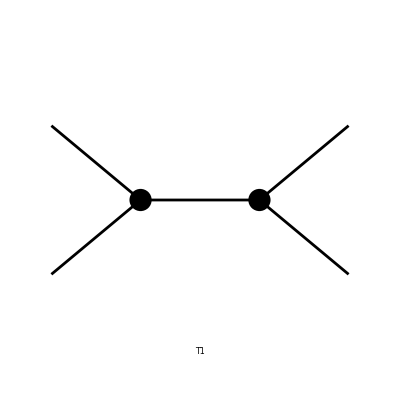

Number of topologies: 1

```mathematica
Paint[topologiesBorn];
Print["Number of topologies: ",topologiesBorn//Length]
```

### 1-Loop

```mathematica
topologies1LCheck=CreateTopologies[1,2->2,ExcludeTopologies->{Tadpoles,WFCorrections}];
topologies1L=excludeTopologies[topologies1LCheck];
(*topologies1L=excludeTopologiesOutgoing[topologies1L];*)
Print["Number of topologies: ",{topologies1LCheck,topologies1L}//Map[Length]]
```

Number of topologies: {42,4}

#### Unfiltered

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

> Top. 2 aebf/cgdf/egefgf.m, 0 diagrams

> Top. 3 aebf/cfdg/egefgf.m, 0 diagrams

> Top. 4 aebf/cgde/fgfege.m, 0 diagrams

> Top. 5 aebf/cedg/fgfege.m, 0 diagrams

> Top. 6 aebe/cfdg/fgfege.m, 0 diagrams

> Top. 7 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 8 aebf/cedg/ehfgfhgh.m, 0 diagrams

> Top. 9 aebf/cfdg/fhegehgh.m, 0 diagrams

> Top. 10 aebf/cgde/ehfgfhgh.m, 0 diagrams

> Top. 11 aebf/cgdf/fhegehgh.m, 0 diagrams

> Top. 12 aebf/cgdg/ghefehfh.m, 0 diagrams

> Top. 13 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 14 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 15 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 16 aebe/cedf/efff.m, 0 diagrams

> Top. 17 aebe/cfde/efff.m, 0 diagrams

> Top. 18 aebe/cfdf/efef.m, 0 diagrams

> Top. 19 aebf/cede/efff.m, 0 diagrams

> Top. 20 aebf/cedf/efef.m, 0 diagrams

> Top. 21 aebf/cfde/efef.m, 0 diagrams

> Top. 22 aebf/cfdf/efee.m, 0 diagrams

> Top. 23 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 24 aebe/cfdg/effggg.m, 0 diagrams

> Top. 25 aebe/cfdg/egfgfg.m, 0 diagrams

> Top. 26 aebe/cfdg/eggfff.m, 0 diagrams

> Top. 27 aebe/cfdg/efgfgf.m, 0 diagrams

> Top. 28 aebe/cfdf/eggfgf.m, 0 diagrams

> Top. 29 aebf/cedf/egfggg.m, 0 diagrams

> Top. 30 aebf/cedg/effggg.m, 0 diagrams

> Top. 31 aebf/cedg/egfgfg.m, 0 diagrams

> Top. 32 aebf/cfde/egfggg.m, 0 diagrams

> Top. 33 aebf/cfdg/efeggg.m, 0 diagrams

> Top. 34 aebf/cfdg/fgegeg.m, 0 diagrams

> Top. 35 aebf/cgde/effggg.m, 0 diagrams

> Top. 36 aebf/cgde/egfgfg.m, 0 diagrams

> Top. 37 aebf/cgdf/efeggg.m, 0 diagrams

> Top. 38 aebf/cgdf/fgegeg.m, 0 diagrams

> Top. 39 aebf/cedg/eggfff.m, 0 diagrams

> Top. 40 aebf/cedg/efgfgf.m, 0 diagrams

> Top. 41 aebf/cedf/eggfgf.m, 0 diagrams

> Top. 42 aebf/cgde/eggfff.m, 0 diagrams

> Top. 43 aebf/cgde/efgfgf.m, 0 diagrams

> Top. 44 aebf/cgdg/egefff.m, 0 diagrams

> Top. 45 aebf/cgdg/gfefef.m, 0 diagrams

> Top. 46 aebf/cfde/eggfgf.m, 0 diagrams

> Top. 47 aebf/cfdf/gfegeg.m, 0 diagrams

> Top. 48 aebf/cfdg/fggeee.m, 0 diagrams

> Top. 49 aebf/cfdg/fegege.m, 0 diagrams

> Top. 50 aebf/cfde/fggege.m, 0 diagrams

> Top. 51 aebf/cgdf/fggeee.m, 0 diagrams

> Top. 52 aebf/cgdf/fegege.m, 0 diagrams

> Top. 53 aebf/cgdg/fgfeee.m, 0 diagrams

> Top. 54 aebf/cgdg/gefefe.m, 0 diagrams

> Top. 55 aebf/cedf/fggege.m, 0 diagrams

> Top. 56 aebf/cede/gefgfg.m, 0 diagrams

> Top. 57 aebe/cfdf/fggege.m, 0 diagrams

> Top. 58 aebe/cfde/gefgfg.m, 0 diagrams

> Top. 59 aebe/cedf/gefgfg.m, 0 diagrams

> Top. 60 aebe/cfdf/egfhghgh.m, 0 diagrams

> Top. 61 aebe/cfdg/effhghgh.m, 0 diagrams

> Top. 62 aebe/cfdg/egghfhfh.m, 0 diagrams

> Top. 63 aebf/cedf/egfhghgh.m, 0 diagrams

> Top. 64 aebf/cedg/effhghgh.m, 0 diagrams

> Top. 65 aebf/cedg/egghfhfh.m, 0 diagrams

> Top. 66 aebf/cfde/egfhghgh.m, 0 diagrams

> Top. 67 aebf/cfdg/efehghgh.m, 0 diagrams

> Top. 68 aebf/cfdg/fggheheh.m, 0 diagrams

> Top. 69 aebf/cgde/effhghgh.m, 0 diagrams

> Top. 70 aebf/cgde/egghfhfh.m, 0 diagrams

> Top. 71 aebf/cgdf/efehghgh.m, 0 diagrams

> Top. 72 aebf/cgdf/fggheheh.m, 0 diagrams

> Top. 73 aebf/cgdg/egehfhfh.m, 0 diagrams

> Top. 74 aebf/cgdg/fgfheheh.m, 0 diagrams

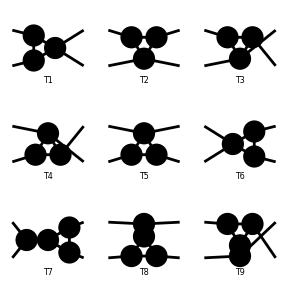

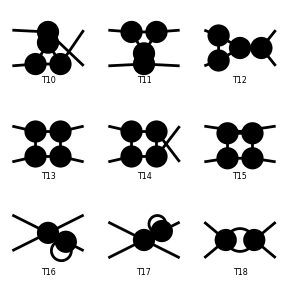

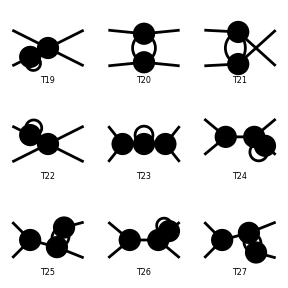

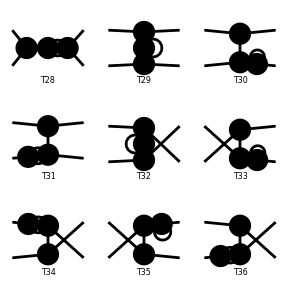

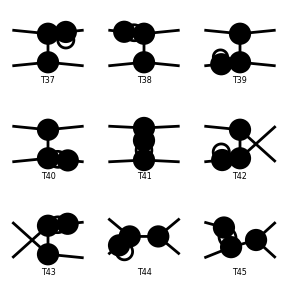

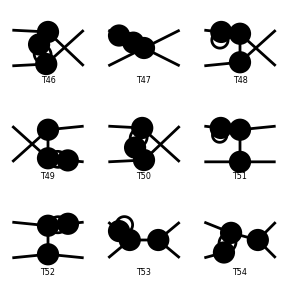

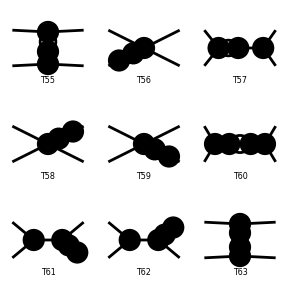

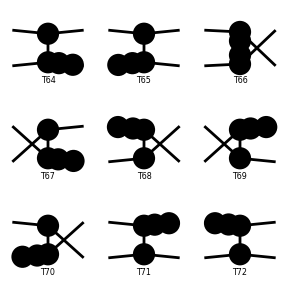

Number of topologies: 74

```mathematica
Paint[topologies1LCheck];
Print["Number of topologies: ",topologies1LCheck//Length]
```

```mathematica
DiagramExtract[topologies1LCheck,61]
```

{Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][7]],Propagator[Internal][Vertex[3][5],Vertex[3][6]],Propagator[Internal][Vertex[3][6],Vertex[3][8]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8]]]}

#### Filtered

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebe/cfdg/egfgfg.m, 0 diagrams

> Top. 3 aebe/cfdg/efgfgf.m, 0 diagrams

> Top. 4 aebe/cfdf/eggfgf.m, 0 diagrams

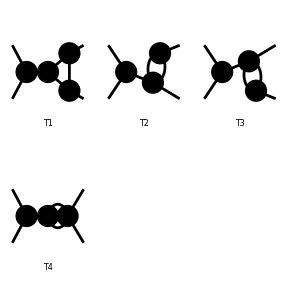

Number of topologies: 4

```mathematica
Paint[topologies1L];
Print["Number of topologies: ",topologies1L//Length]
```

```mathematica
DiagramExtract[topologies1L,8]
```

{Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][7]],Propagator[Internal][Vertex[3][6],Vertex[3][8]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8]]]}

### 2-Loop

```mathematica
topologies2LCheck=CreateTopologies[2,2->2,ExcludeTopologies->{Tadpoles,WFCorrections}];
topologies2L=excludeTopologies[topologies2LCheck];
Print["Number of topologies: ",{topologies2LCheck,topologies2L}//Map[Length]]
```

Number of topologies: {640,40}

```mathematica
topologies2LTP=excludeTopologies[CreateTopologies[2,2->2,ExcludeTopologies->{WFCorrections,Loops[Except[1]]}]];
topologies2LSE=excludeTopologies[CreateTopologies[2,2->2,ExcludeTopologies->{Tadpoles,WFCorrections,Loops[Except[2]]}]];
topologies2LTR=excludeTopologies[CreateTopologies[2,2->2,ExcludeTopologies->{Tadpoles,WFCorrections, Loops[Except[3]]}]];
topologies2LBX=excludeTopologies[CreateTopologies[2,2->2,ExcludeTopologies->{Tadpoles,WFCorrections,Loops[Except[4]]}]];
```

#### Unfiltered

> Top. 1 aebf/c1d2/e2e1f2f121.m, 0 diagrams

> Top. 2 aeb1/cfd2/e2e1f2f121.m, 0 diagrams

> Top. 3 aeb1/c2df/e2e1f2f121.m, 0 diagrams

> Top. 4 aeb1/cfdf/2e212fe11f.m, 0 diagrams

> Top. 5 aebf/c1df/2e212fe11f.m, 0 diagrams

> Top. 6 aebf/cfd1/2e212fe11f.m, 0 diagrams

> Top. 7 VFlip[aeb1/c2df/e2e1f2f121.m], 0 diagrams

> Top. 8 VFlip[aeb1/cfd2/e2e1f2f121.m], 0 diagrams

> Top. 9 VFlip[aeb1/cfdf/2e212fe11f.m], 0 diagrams

> Top. 10 HFlip[aebf/c1d2/e2e1f2f121.m], 0 diagrams

> Top. 11 HFlip[aebf/c1df/2e212fe11f.m], 0 diagrams

> Top. 12 HFlip[VFlip[aebf/cfd1/2e212fe11f.m]], 0 diagrams

> Top. 13 VFlip[aebf/cfd1/2e212fe11f.m], 0 diagrams

> Top. 14 VFlip[aebf/c1df/2e212fe11f.m], 0 diagrams

> Top. 15 HFlip[aebf/cfd1/2e212fe11f.m], 0 diagrams

> Top. 16 VFlip[HFlip[aebf/c1df/2e212fe11f.m]], 0 diagrams

> Top. 17 HFlip[aeb1/cfdf/2e212fe11f.m], 0 diagrams

> Top. 18 VFlip[HFlip[aeb1/cfdf/2e212fe11f.m]], 0 diagrams

> Top. 19 aebe/cfdg/e12f2g21f1g1.m, 0 diagrams

> Top. 20 aebe/cfd1/eg2f2g21f1g1.m, 0 diagrams

> Top. 21 VFlip[aebe/cfd1/eg2f2g21f1g1.m], 0 diagrams

> Top. 22 aebf/cedg/e12f2g21f1g1.m, 0 diagrams

> Top. 23 aebf/ced1/eg2f2g21f1g1.m, 0 diagrams

> Top. 24 aebf/cfdg/f12e2g21e1g1.m, 0 diagrams

> Top. 25 aebf/cfd1/fg2e2g21e1g1.m, 0 diagrams

> Top. 26 VFlip[aebf/cfdg/f12e2g21e1g1.m], 0 diagrams

> Top. 27 VFlip[aebf/cedg/e12f2g21f1g1.m], 0 diagrams

> Top. 28 HFlip[aebe/cfdg/e12f2g21f1g1.m], 0 diagrams

> Top. 29 aebf/cgdh/efeifighgihi.m, 0 diagrams

> Top. 30 aebf/cgdh/egeifhfigihi.m, 0 diagrams

> Top. 31 aebf/cgdh/eheifgfigihi.m, 0 diagrams

> Top. 32 aebf/cgd1/2e2f2ge1f1g1.m, 0 diagrams

> Top. 33 aebf/cgd1/2e2f21e1fgg1.m, 0 diagrams

> Top. 34 aebf/cgd1/2e2g21e1fgf1.m, 0 diagrams

> Top. 35 aebf/cgd1/ef2e2g21f1g1.m, 0 diagrams

> Top. 36 aebf/cgd1/efe12f2g21g1.m, 0 diagrams

> Top. 37 aebf/cgd1/eg2e2f21f1g1.m, 0 diagrams

> Top. 38 aebf/cgd1/ege12f2g21f1.m, 0 diagrams

> Top. 39 VFlip[aebf/cfd1/fg2e2g21e1g1.m], 0 diagrams

> Top. 40 VFlip[aebf/ced1/eg2f2g21f1g1.m], 0 diagrams

> Top. 41 VFlip[aebf/cgd1/2e2f2ge1f1g1.m], 0 diagrams

> Top. 42 VFlip[aebf/cgd1/eg2e2f21f1g1.m], 0 diagrams

> Top. 43 VFlip[aebf/cgd1/ege12f2g21f1.m], 0 diagrams

> Top. 44 VFlip[aebf/cgd1/efe12f2g21g1.m], 0 diagrams

> Top. 45 VFlip[aebf/cgd1/ef2e2g21f1g1.m], 0 diagrams

> Top. 46 VFlip[aebf/cgd1/2e2f21e1fgg1.m], 0 diagrams

> Top. 47 VFlip[aebf/cgd1/2e2g21e1fgf1.m], 0 diagrams

> Top. 48 aebf/cgdg/1e212e2f1gfg.m, 0 diagrams

> Top. 49 VFlip[aebf/cgdg/1e212e2f1gfg.m], 0 diagrams

> Top. 50 aebf/cgdg/ef1e212f2g1g.m, 0 diagrams

> Top. 51 HFlip[aebf/ced1/eg2f2g21f1g1.m], 0 diagrams

> Top. 52 HFlip[aebf/cfd1/fg2e2g21e1g1.m], 0 diagrams

> Top. 53 HFlip[aebe/cfd1/eg2f2g21f1g1.m], 0 diagrams

> Top. 54 HFlip[aebf/cgd1/2e2f2ge1f1g1.m], 0 diagrams

> Top. 55 HFlip[aebf/cgd1/ef2e2g21f1g1.m], 0 diagrams

> Top. 56 HFlip[aebf/cgd1/efe12f2g21g1.m], 0 diagrams

> Top. 57 HFlip[aebf/cgd1/ege12f2g21f1.m], 0 diagrams

> Top. 58 HFlip[aebf/cgd1/eg2e2f21f1g1.m], 0 diagrams

> Top. 59 HFlip[aebf/cgd1/2e2g21e1fgf1.m], 0 diagrams

> Top. 60 HFlip[aebf/cgd1/2e2f21e1fgg1.m], 0 diagrams

> Top. 61 aebf/cgdf/1e1g212e2fgf.m, 0 diagrams

> Top. 62 aebf/cgdf/1e1g212g2fef.m, 0 diagrams

> Top. 63 aebf/cgdf/eg1e212g2f1f.m, 0 diagrams

> Top. 64 aebf/cfdg/1e1g212e2fgf.m, 0 diagrams

> Top. 65 HFlip[VFlip[aebf/cfdg/1e1g212e2fgf.m]], 0 diagrams

> Top. 66 aebf/cfdg/eg1e212g2f1f.m, 0 diagrams

> Top. 67 VFlip[HFlip[aebf/cfd1/fg2e2g21e1g1.m]], 0 diagrams

> Top. 68 VFlip[HFlip[aebf/ced1/eg2f2g21f1g1.m]], 0 diagrams

> Top. 69 VFlip[HFlip[aebe/cfd1/eg2f2g21f1g1.m]], 0 diagrams

> Top. 70 VFlip[HFlip[aebf/cgd1/2e2f2ge1f1g1.m]], 0 diagrams

> Top. 71 VFlip[HFlip[aebf/cgd1/efe12f2g21g1.m]], 0 diagrams

> Top. 72 VFlip[HFlip[aebf/cgd1/ef2e2g21f1g1.m]], 0 diagrams

> Top. 73 VFlip[HFlip[aebf/cgd1/2e2g21e1fgf1.m]], 0 diagrams

> Top. 74 VFlip[HFlip[aebf/cgd1/2e2f21e1fgg1.m]], 0 diagrams

> Top. 75 VFlip[HFlip[aebf/cgd1/ege12f2g21f1.m]], 0 diagrams

> Top. 76 VFlip[HFlip[aebf/cgd1/eg2e2f21f1g1.m]], 0 diagrams

> Top. 77 aebf/cgde/1f1g212f2ege.m, 0 diagrams

> Top. 78 HFlip[VFlip[aebf/cgde/1f1g212f2ege.m]], 0 diagrams

> Top. 79 VFlip[aebf/cfdg/eg1e212g2f1f.m], 0 diagrams

> Top. 80 HFlip[VFlip[aebf/cgdf/1e1g212g2fef.m]], 0 diagrams

> Top. 81 VFlip[aebf/cgdf/1e1g212g2fef.m], 0 diagrams

> Top. 82 VFlip[aebf/cgdf/eg1e212g2f1f.m], 0 diagrams

> Top. 83 HFlip[aebf/cgdg/1e212e2f1gfg.m], 0 diagrams

> Top. 84 HFlip[VFlip[aebf/cgdg/1e212e2f1gfg.m]], 0 diagrams

> Top. 85 HFlip[aebf/cgdg/ef1e212f2g1g.m], 0 diagrams

> Top. 86 aebe/cfdg/eh1f1g212f2hgh.m, 0 diagrams

> Top. 87 aebe/cfdg/ehfg1f1h212g2h.m, 0 diagrams

> Top. 88 aebe/cfdg/ehfh1f1g212g2h.m, 0 diagrams

> Top. 89 aebf/cedg/eh1f1g212f2hgh.m, 0 diagrams

> Top. 90 aebf/cedg/ehfg1f1h212g2h.m, 0 diagrams

> Top. 91 aebf/cedg/ehfh1f1g212g2h.m, 0 diagrams

> Top. 92 aebf/cfdg/fh1e1g212e2hgh.m, 0 diagrams

> Top. 93 aebf/cfdg/fheg1e1h212g2h.m, 0 diagrams

> Top. 94 HFlip[VFlip[aebf/cfdg/fh1e1g212e2hgh.m]], 0 diagrams

> Top. 95 aebf/cgde/eh1f1g212f2hgh.m, 0 diagrams

> Top. 96 VFlip[aebf/cfdg/fheg1e1h212g2h.m], 0 diagrams

> Top. 97 HFlip[VFlip[aebf/cgde/eh1f1g212f2hgh.m]], 0 diagrams

> Top. 98 HFlip[VFlip[aebf/cedg/ehfh1f1g212g2h.m]], 0 diagrams

> Top. 99 VFlip[aebf/cedg/ehfg1f1h212g2h.m], 0 diagrams

> Top. 100 VFlip[aebf/cedg/ehfh1f1g212g2h.m], 0 diagrams

> Top. 101 HFlip[aebe/cfdg/eh1f1g212f2hgh.m], 0 diagrams

> Top. 102 HFlip[aebe/cfdg/ehfg1f1h212g2h.m], 0 diagrams

> Top. 103 VFlip[HFlip[aebe/cfdg/eh1f1g212f2hgh.m]], 0 diagrams

> Top. 104 aebf/cgdh/212f2g1e1hehfg.m, 0 diagrams

> Top. 105 aebf/cgdh/212f2h1e1gegfh.m, 0 diagrams

> Top. 106 aebf/cgdh/212g2h1e1fefgh.m, 0 diagrams

> Top. 107 aebf/cgdh/1e1f1h2e2f2ggh.m, 0 diagrams

> Top. 108 aebf/cgdh/1e1g212e2ffhgh.m, 0 diagrams

> Top. 109 aebf/cgdh/1e1g212e2hfgfh.m, 0 diagrams

> Top. 110 aebf/cgdh/1e1g1h2e2f2gfh.m, 0 diagrams

> Top. 111 aebf/cgdh/1e1g1h2e2f2hfg.m, 0 diagrams

> Top. 112 aebf/cgdh/1e1h212e2ffggh.m, 0 diagrams

> Top. 113 aebf/cgdh/ef1e1g212f2hgh.m, 0 diagrams

> Top. 114 aebf/cgdh/ef1e1g212g2hfh.m, 0 diagrams

> Top. 115 HFlip[aebf/cgdh/1e1f1h2e2f2ggh.m], 0 diagrams

> Top. 116 aebf/cgdh/ef1e1h212f2ggh.m, 0 diagrams

> Top. 117 VFlip[aebf/cgdh/efeh1f1g212g2h.m], 0 diagrams

> Top. 118 VFlip[aebf/cgdh/ef1e1g212g2hfh.m], 0 diagrams

> Top. 119 aebf/cgdh/efeh1f1g212g2h.m, 0 diagrams

> Top. 120 VFlip[aebf/cgdh/1e1g212e2ffhgh.m], 0 diagrams

> Top. 121 aebf/cgdh/eg1e1f212g2hfh.m, 0 diagrams

> Top. 122 VFlip[aebf/cgdh/1e1g1h2e2f2gfh.m], 0 diagrams

> Top. 123 aebf/cgdh/eg1e1h212f2gfh.m, 0 diagrams

> Top. 124 aebf/cgdh/eg1e1h212f2hfg.m, 0 diagrams

> Top. 125 VFlip[aebf/cgdh/1e1g212e2hfgfh.m], 0 diagrams

> Top. 126 VFlip[aebf/cgdh/1e1h212e2ffggh.m], 0 diagrams

> Top. 127 aebf/cgdh/eh1e1f212g2hfg.m, 0 diagrams

> Top. 128 VFlip[aebf/cgdh/1e1g1h2e2f2hfg.m], 0 diagrams

> Top. 129 VFlip[aebf/cgdh/eg1e1h212f2hfg.m], 0 diagrams

> Top. 130 aebf/cgdh/eh1e1g212f2hfg.m, 0 diagrams

> Top. 131 a1b2/cede/21212e1e.m, 0 diagrams

> Top. 132 a1be/c2de/21212e1e.m, 0 diagrams

> Top. 133 a1be/ced2/21212e1e.m, 0 diagrams

> Top. 134 VFlip[a1be/ced2/21212e1e.m], 0 diagrams

> Top. 135 VFlip[a1be/c2de/21212e1e.m], 0 diagrams

> Top. 136 HFlip[a1b2/cede/21212e1e.m], 0 diagrams

> Top. 137 aebe/cfdf/efegfggg.m, 0 diagrams

> Top. 138 aebf/cedf/efegfggg.m, 0 diagrams

> Top. 139 aebf/cfde/efegfggg.m, 0 diagrams

> Top. 140 aebe/cfd1/e2f2f12121.m, 0 diagrams

> Top. 141 aebe/cfdg/egfgfhghhh.m, 0 diagrams

> Top. 142 VFlip[aebe/cfd1/e2f2f12121.m], 0 diagrams

> Top. 143 aebe/c1d2/eff2f12121.m, 0 diagrams

> Top. 144 aebe/c1df/ef21212f1f.m, 0 diagrams

> Top. 145 VFlip[aebe/cfdg/egfgfhghhh.m], 0 diagrams

> Top. 146 VFlip[aebe/c1df/ef21212f1f.m], 0 diagrams

> Top. 147 aebe/cfdf/eggfghfhhh.m, 0 diagrams

> Top. 148 aebe/cfdf/e121212f1f.m, 0 diagrams

> Top. 149 aebf/ced1/e2f2f12121.m, 0 diagrams

> Top. 150 aebf/cedg/egfgfhghhh.m, 0 diagrams

> Top. 151 aebf/cfd1/f2e2e12121.m, 0 diagrams

> Top. 152 aebf/cfdg/fgegehghhh.m, 0 diagrams

> Top. 153 VFlip[aebf/cfd1/f2e2e12121.m], 0 diagrams

> Top. 154 VFlip[aebf/ced1/e2f2f12121.m], 0 diagrams

> Top. 155 aebf/c1d2/efe2f12121.m, 0 diagrams

> Top. 156 aebf/c1d2/efe1f22121.m, 0 diagrams

> Top. 157 VFlip[aebf/cfdg/fgegehghhh.m], 0 diagrams

> Top. 158 VFlip[aebf/cedg/egfgfhghhh.m], 0 diagrams

> Top. 159 aebf/cgdg/efegfhghhh.m, 0 diagrams

> Top. 160 VFlip[aebf/cgdg/efegfhghhh.m], 0 diagrams

> Top. 161 aebf/cgdg/efehfhghgh.m, 0 diagrams

> Top. 162 aebf/cgdg/egehfgfhhh.m, 0 diagrams

> Top. 163 aebf/cgdg/egehfhfhgh.m, 0 diagrams

> Top. 164 VFlip[aebf/cgdg/egehfhfhgh.m], 0 diagrams

> Top. 165 HFlip[aebf/ced1/e2f2f12121.m], 0 diagrams

> Top. 166 aeb1/ced2/eff2f12121.m, 0 diagrams

> Top. 167 aeb1/cedf/ef21212f1f.m, 0 diagrams

> Top. 168 HFlip[aebf/cfd1/f2e2e12121.m], 0 diagrams

> Top. 169 HFlip[aebe/cfd1/e2f2f12121.m], 0 diagrams

> Top. 170 aeb1/cfd2/efe2f12121.m, 0 diagrams

> Top. 171 aeb1/cfd2/efe1f22121.m, 0 diagrams

> Top. 172 aeb1/c2de/eff2f12121.m, 0 diagrams

> Top. 173 aeb1/c2df/efe2f12121.m, 0 diagrams

> Top. 174 aeb1/c2df/efe1f22121.m, 0 diagrams

> Top. 175 aeb1/cfde/ef21212f1f.m, 0 diagrams

> Top. 176 aeb1/cfdf/2e2121ef1f.m, 0 diagrams

> Top. 177 aeb1/cfdf/e1ef21212f.m, 0 diagrams

> Top. 178 HFlip[aebf/cedg/egfgfhghhh.m], 0 diagrams

> Top. 179 HFlip[aeb1/cedf/ef21212f1f.m], 0 diagrams

> Top. 180 aebf/cedf/eggfghfhhh.m, 0 diagrams

> Top. 181 aebf/cedf/e121212f1f.m, 0 diagrams

> Top. 182 HFlip[aebf/cfdg/fgegehghhh.m], 0 diagrams

> Top. 183 HFlip[aebe/cfdg/egfgfhghhh.m], 0 diagrams

> Top. 184 aebf/cgdf/egefghfhhh.m, 0 diagrams

> Top. 185 HFlip[aebf/cgdf/egefghfhhh.m], 0 diagrams

> Top. 186 aebf/cgdf/egehghfhfh.m, 0 diagrams

> Top. 187 aebf/cgdf/efehgfghhh.m, 0 diagrams

> Top. 188 aebf/cgdf/efehghghfh.m, 0 diagrams

> Top. 189 HFlip[aebf/cgdf/efehghghfh.m], 0 diagrams

> Top. 190 HFlip[VFlip[aeb1/cfde/ef21212f1f.m]], 0 diagrams

> Top. 191 aebf/c1df/2e2121ef1f.m, 0 diagrams

> Top. 192 aebf/c1df/e1ef21212f.m, 0 diagrams

> Top. 193 aebf/cfde/eggfghfhhh.m, 0 diagrams

> Top. 194 aebf/cfde/e121212f1f.m, 0 diagrams

> Top. 195 aebf/cfdg/egefghfhhh.m, 0 diagrams

> Top. 196 HFlip[VFlip[aebf/cfdg/egefghfhhh.m]], 0 diagrams

> Top. 197 aebf/cfdg/egehghfhfh.m, 0 diagrams

> Top. 198 aebf/cfdg/efehgfghhh.m, 0 diagrams

> Top. 199 aebf/cfdg/efehghghfh.m, 0 diagrams

> Top. 200 HFlip[VFlip[aebf/cfdg/efehghghfh.m]], 0 diagrams

> Top. 201 aebf/cfd1/2e2121ef1f.m, 0 diagrams

> Top. 202 aebf/cfd1/e1ef21212f.m, 0 diagrams

> Top. 203 VFlip[HFlip[aebf/cfd1/f2e2e12121.m]], 0 diagrams

> Top. 204 VFlip[aeb1/c2de/eff2f12121.m], 0 diagrams

> Top. 205 VFlip[aeb1/cfde/ef21212f1f.m], 0 diagrams

> Top. 206 VFlip[HFlip[aebf/ced1/e2f2f12121.m]], 0 diagrams

> Top. 207 VFlip[HFlip[aebe/cfd1/e2f2f12121.m]], 0 diagrams

> Top. 208 VFlip[aeb1/c2df/efe2f12121.m], 0 diagrams

> Top. 209 VFlip[aeb1/c2df/efe1f22121.m], 0 diagrams

> Top. 210 VFlip[aeb1/ced2/eff2f12121.m], 0 diagrams

> Top. 211 VFlip[aeb1/cfd2/efe2f12121.m], 0 diagrams

> Top. 212 VFlip[aeb1/cfd2/efe1f22121.m], 0 diagrams

> Top. 213 VFlip[aeb1/cedf/ef21212f1f.m], 0 diagrams

> Top. 214 VFlip[aeb1/cfdf/2e2121ef1f.m], 0 diagrams

> Top. 215 VFlip[aeb1/cfdf/e1ef21212f.m], 0 diagrams

> Top. 216 HFlip[aebe/c1d2/eff2f12121.m], 0 diagrams

> Top. 217 HFlip[aebf/c1d2/efe2f12121.m], 0 diagrams

> Top. 218 HFlip[aebf/c1d2/efe1f22121.m], 0 diagrams

> Top. 219 HFlip[aebe/c1df/ef21212f1f.m], 0 diagrams

> Top. 220 HFlip[aebf/c1df/2e2121ef1f.m], 0 diagrams

> Top. 221 HFlip[aebf/c1df/e1ef21212f.m], 0 diagrams

> Top. 222 HFlip[VFlip[aebf/cfd1/2e2121ef1f.m]], 0 diagrams

> Top. 223 HFlip[VFlip[aebf/cfd1/e1ef21212f.m]], 0 diagrams

> Top. 224 VFlip[HFlip[aebf/cfdg/fgegehghhh.m]], 0 diagrams

> Top. 225 HFlip[aeb1/cfde/ef21212f1f.m], 0 diagrams

> Top. 226 VFlip[aebf/cfde/eggfghfhhh.m], 0 diagrams

> Top. 227 VFlip[aebf/cfde/e121212f1f.m], 0 diagrams

> Top. 228 VFlip[HFlip[aebf/cedg/egfgfhghhh.m]], 0 diagrams

> Top. 229 VFlip[HFlip[aebe/cfdg/egfgfhghhh.m]], 0 diagrams

> Top. 230 VFlip[aebf/cfdg/egefghfhhh.m], 0 diagrams

> Top. 231 HFlip[aebf/cfdg/egefghfhhh.m], 0 diagrams

> Top. 232 VFlip[aebf/cfdg/egehghfhfh.m], 0 diagrams

> Top. 233 VFlip[aebf/cfdg/efehgfghhh.m], 0 diagrams

> Top. 234 VFlip[aebf/cfdg/efehghghfh.m], 0 diagrams

> Top. 235 HFlip[aebf/cfdg/efehghghfh.m], 0 diagrams

> Top. 236 VFlip[HFlip[aeb1/cedf/ef21212f1f.m]], 0 diagrams

> Top. 237 VFlip[aebf/cfd1/2e2121ef1f.m], 0 diagrams

> Top. 238 VFlip[aebf/cfd1/e1ef21212f.m], 0 diagrams

> Top. 239 VFlip[aebf/cedf/eggfghfhhh.m], 0 diagrams

> Top. 240 VFlip[aebf/cedf/e121212f1f.m], 0 diagrams

> Top. 241 VFlip[aebf/cgdf/egefghfhhh.m], 0 diagrams

> Top. 242 VFlip[HFlip[aebf/cgdf/egefghfhhh.m]], 0 diagrams

> Top. 243 VFlip[aebf/cgdf/egehghfhfh.m], 0 diagrams

> Top. 244 VFlip[aebf/cgdf/efehgfghhh.m], 0 diagrams

> Top. 245 VFlip[aebf/cgdf/efehghghfh.m], 0 diagrams

> Top. 246 VFlip[HFlip[aebf/cgdf/efehghghfh.m]], 0 diagrams

> Top. 247 VFlip[aebf/c1df/2e2121ef1f.m], 0 diagrams

> Top. 248 VFlip[aebf/c1df/e1ef21212f.m], 0 diagrams

> Top. 249 VFlip[HFlip[aebe/c1df/ef21212f1f.m]], 0 diagrams

> Top. 250 HFlip[aebf/cfd1/2e2121ef1f.m], 0 diagrams

> Top. 251 HFlip[aebf/cfd1/e1ef21212f.m], 0 diagrams

> Top. 252 VFlip[HFlip[aebf/c1df/2e2121ef1f.m]], 0 diagrams

> Top. 253 VFlip[HFlip[aebf/c1df/e1ef21212f.m]], 0 diagrams

> Top. 254 HFlip[aebe/cfdf/eggfghfhhh.m], 0 diagrams

> Top. 255 HFlip[aebe/cfdf/e121212f1f.m], 0 diagrams

> Top. 256 HFlip[aebf/cgdg/efegfhghhh.m], 0 diagrams

> Top. 257 VFlip[HFlip[aebf/cgdg/efegfhghhh.m]], 0 diagrams

> Top. 258 HFlip[aebf/cgdg/efehfhghgh.m], 0 diagrams

> Top. 259 HFlip[aebf/cgdg/egehfgfhhh.m], 0 diagrams

> Top. 260 HFlip[aebf/cgdg/egehfhfhgh.m], 0 diagrams

> Top. 261 VFlip[HFlip[aebf/cgdg/egehfhfhgh.m]], 0 diagrams

> Top. 262 HFlip[aeb1/cfdf/2e2121ef1f.m], 0 diagrams

> Top. 263 HFlip[aeb1/cfdf/e1ef21212f.m], 0 diagrams

> Top. 264 VFlip[HFlip[aeb1/cfdf/2e2121ef1f.m]], 0 diagrams

> Top. 265 VFlip[HFlip[aeb1/cfdf/e1ef21212f.m]], 0 diagrams

> Top. 266 aebe/cfdf/21212e1fef.m, 0 diagrams

> Top. 267 aebe/cfdf/212e2f1e1f.m, 0 diagrams

> Top. 268 aebf/cedf/21212e1fef.m, 0 diagrams

> Top. 269 aebf/cedf/212e2f1e1f.m, 0 diagrams

> Top. 270 aebf/cfde/21212e1fef.m, 0 diagrams

> Top. 271 aebf/cfde/212e2f1e1f.m, 0 diagrams

> Top. 272 aebe/cfdf/egfhghgihiii.m, 0 diagrams

> Top. 273 aebe/cfdf/egf12g2121g1.m, 0 diagrams

> Top. 274 HFlip[aebe/cfdf/egf12g2121g1.m], 0 diagrams

> Top. 275 aebe/cfdg/ehfgfhgihiii.m, 0 diagrams

> Top. 276 VFlip[aebe/cfdg/ehfgfhgihiii.m], 0 diagrams

> Top. 277 aebe/cfdg/ehfgfigihihi.m, 0 diagrams

> Top. 278 aebe/cfdg/ehfhfighgiii.m, 0 diagrams

> Top. 279 aebe/cfdg/ehfhfigigihi.m, 0 diagrams

> Top. 280 VFlip[aebe/cfdg/ehfhfigigihi.m], 0 diagrams

> Top. 281 aebe/cfdg/e1212f2gfg11.m, 0 diagrams

> Top. 282 aebe/cfdg/e1fg2f2121g1.m, 0 diagrams

> Top. 283 VFlip[aebe/cfdg/e1fg2f2121g1.m], 0 diagrams

> Top. 284 aebe/cfd1/egfg2f2121g1.m, 0 diagrams

> Top. 285 aebe/cfd1/egfgf12g2121.m, 0 diagrams

> Top. 286 aebe/cfdg/eg1f21212gfg.m, 0 diagrams

> Top. 287 aebe/cfdg/eg1f212f2g1g.m, 0 diagrams

> Top. 288 VFlip[aebe/cfd1/egfg2f2121g1.m], 0 diagrams

> Top. 289 VFlip[aebe/cfd1/egfgf12g2121.m], 0 diagrams

> Top. 290 VFlip[aebe/cfdg/eg1f21212gfg.m], 0 diagrams

> Top. 291 VFlip[aebe/cfdg/eg1f212f2g1g.m], 0 diagrams

> Top. 292 aebe/cfdf/eg1g21212fgf.m, 0 diagrams

> Top. 293 aebe/cfdf/eg1g212g2f1f.m, 0 diagrams

> Top. 294 aebf/cedf/egfhghgihiii.m, 0 diagrams

> Top. 295 aebf/cedf/egf12g2121g1.m, 0 diagrams

> Top. 296 VFlip[aebf/cedf/egf12g2121g1.m], 0 diagrams

> Top. 297 aebf/cedg/ehfgfhgihiii.m, 0 diagrams

> Top. 298 HFlip[aebf/cedg/ehfgfhgihiii.m], 0 diagrams

> Top. 299 aebf/cedg/ehfgfigihihi.m, 0 diagrams

> Top. 300 aebf/cedg/ehfhfighgiii.m, 0 diagrams

> Top. 301 aebf/cedg/ehfhfigigihi.m, 0 diagrams

> Top. 302 HFlip[aebf/cedg/ehfhfigigihi.m], 0 diagrams

> Top. 303 aebf/cedg/e1212f2gfg11.m, 0 diagrams

> Top. 304 aebf/cedg/e1fg2f2121g1.m, 0 diagrams

> Top. 305 HFlip[aebf/cedg/e1fg2f2121g1.m], 0 diagrams

> Top. 306 aebf/ced1/egfg2f2121g1.m, 0 diagrams

> Top. 307 aebf/ced1/egfgf12g2121.m, 0 diagrams

> Top. 308 aebf/cedg/eg1f21212gfg.m, 0 diagrams

> Top. 309 aebf/cedg/eg1f212f2g1g.m, 0 diagrams

> Top. 310 aebf/cfde/egfhghgihiii.m, 0 diagrams

> Top. 311 aebf/cfde/egf12g2121g1.m, 0 diagrams

> Top. 312 VFlip[aebf/cfde/egf12g2121g1.m], 0 diagrams

> Top. 313 aebf/cfdg/fhegehgihiii.m, 0 diagrams

> Top. 314 HFlip[VFlip[aebf/cfdg/fhegehgihiii.m]], 0 diagrams

> Top. 315 aebf/cfdg/fhegeigihihi.m, 0 diagrams

> Top. 316 aebf/cfdg/fheheighgiii.m, 0 diagrams

> Top. 317 aebf/cfdg/fheheigigihi.m, 0 diagrams

> Top. 318 HFlip[VFlip[aebf/cfdg/fheheigigihi.m]], 0 diagrams

> Top. 319 aebf/cfdg/f1212e2geg11.m, 0 diagrams

> Top. 320 aebf/cfdg/f1eg2e2121g1.m, 0 diagrams

> Top. 321 HFlip[VFlip[aebf/cfdg/f1eg2e2121g1.m]], 0 diagrams

> Top. 322 aebf/cfd1/fgeg2e2121g1.m, 0 diagrams

> Top. 323 aebf/cfd1/fgege12g2121.m, 0 diagrams

> Top. 324 aebf/cfdg/fg1e21212geg.m, 0 diagrams

> Top. 325 aebf/cfdg/fg1e212e2g1g.m, 0 diagrams

> Top. 326 VFlip[aebf/cfdg/fhegehgihiii.m], 0 diagrams

> Top. 327 HFlip[aebf/cfdg/fhegehgihiii.m], 0 diagrams

> Top. 328 VFlip[aebf/cfdg/fhegeigihihi.m], 0 diagrams

> Top. 329 VFlip[aebf/cfdg/fheheighgiii.m], 0 diagrams

> Top. 330 VFlip[aebf/cfdg/fheheigigihi.m], 0 diagrams

> Top. 331 HFlip[aebf/cfdg/fheheigigihi.m], 0 diagrams

> Top. 332 VFlip[aebf/cfdg/f1212e2geg11.m], 0 diagrams

> Top. 333 VFlip[aebf/cfdg/f1eg2e2121g1.m], 0 diagrams

> Top. 334 HFlip[aebf/cfdg/f1eg2e2121g1.m], 0 diagrams

> Top. 335 VFlip[aebf/cedg/ehfgfhgihiii.m], 0 diagrams

> Top. 336 VFlip[HFlip[aebf/cedg/ehfgfhgihiii.m]], 0 diagrams

> Top. 337 VFlip[aebf/cedg/ehfgfigihihi.m], 0 diagrams

> Top. 338 VFlip[aebf/cedg/ehfhfighgiii.m], 0 diagrams

> Top. 339 VFlip[aebf/cedg/ehfhfigigihi.m], 0 diagrams

> Top. 340 VFlip[HFlip[aebf/cedg/ehfhfigigihi.m]], 0 diagrams

> Top. 341 VFlip[aebf/cedg/e1212f2gfg11.m], 0 diagrams

> Top. 342 VFlip[aebf/cedg/e1fg2f2121g1.m], 0 diagrams

> Top. 343 VFlip[HFlip[aebf/cedg/e1fg2f2121g1.m]], 0 diagrams

> Top. 344 HFlip[aebe/cfdg/ehfgfhgihiii.m], 0 diagrams

> Top. 345 VFlip[HFlip[aebe/cfdg/ehfgfhgihiii.m]], 0 diagrams

> Top. 346 HFlip[aebe/cfdg/ehfgfigihihi.m], 0 diagrams

> Top. 347 HFlip[aebe/cfdg/ehfhfighgiii.m], 0 diagrams

> Top. 348 HFlip[aebe/cfdg/ehfhfigigihi.m], 0 diagrams

> Top. 349 VFlip[HFlip[aebe/cfdg/ehfhfigigihi.m]], 0 diagrams

> Top. 350 HFlip[aebe/cfdg/e1212f2gfg11.m], 0 diagrams

> Top. 351 HFlip[aebe/cfdg/e1fg2f2121g1.m], 0 diagrams

> Top. 352 VFlip[HFlip[aebe/cfdg/e1fg2f2121g1.m]], 0 diagrams

> Top. 353 aebf/cgdh/efegfhgihiii.m, 0 diagrams

> Top. 354 aebf/cgdh/efegfighhiii.m, 0 diagrams

> Top. 355 aebf/cgdh/efegfigihihi.m, 0 diagrams

> Top. 356 aebf/cgdh/efehfggihiii.m, 0 diagrams

> Top. 357 aebf/cgdh/efehfighgiii.m, 0 diagrams

> Top. 358 aebf/cgdh/efehfigigihi.m, 0 diagrams

> Top. 359 VFlip[aebf/cgdh/efehfighgiii.m], 0 diagrams

> Top. 360 VFlip[aebf/cgdh/efehfigigihi.m], 0 diagrams

> Top. 361 VFlip[aebf/cgdh/efegfighhiii.m], 0 diagrams

> Top. 362 VFlip[aebf/cgdh/efegfigihihi.m], 0 diagrams

> Top. 363 aebf/cgdh/egehfgfihiii.m, 0 diagrams

> Top. 364 aebf/cgdh/egehfhfigiii.m, 0 diagrams

> Top. 365 aebf/cgdh/egehfifigihi.m, 0 diagrams

> Top. 366 VFlip[aebf/cgdh/egehfhfigiii.m], 0 diagrams

> Top. 367 HFlip[aebf/cgdh/egehfifigihi.m], 0 diagrams

> Top. 368 HFlip[aebf/cgdh/efegfhgihiii.m], 0 diagrams

> Top. 369 HFlip[aebf/cgdh/efegfigihihi.m], 0 diagrams

> Top. 370 VFlip[aebf/cgdh/egehfgfihiii.m], 0 diagrams

> Top. 371 HFlip[aebf/cgdh/efehfggihiii.m], 0 diagrams

> Top. 372 VFlip[HFlip[aebf/cgdh/egehfifigihi.m]], 0 diagrams

> Top. 373 HFlip[VFlip[aebf/cgdh/efehfigigihi.m]], 0 diagrams

> Top. 374 VFlip[aebf/cgdh/egehfifigihi.m], 0 diagrams

> Top. 375 HFlip[aebf/cgdh/efehfigigihi.m], 0 diagrams

> Top. 376 VFlip[HFlip[aebf/cgdh/efegfigihihi.m]], 0 diagrams

> Top. 377 aebf/cgd1/212e2fefg1g1.m, 0 diagrams

> Top. 378 aebf/cgd1/212e2gegf1f1.m, 0 diagrams

> Top. 379 aebf/cgd1/212f2ge1e1fg.m, 0 diagrams

> Top. 380 aebf/cgd1/ef2e2121fgg1.m, 0 diagrams

> Top. 381 aebf/cgd1/efeg2f2121g1.m, 0 diagrams

> Top. 382 aebf/cgd1/efegf12g2121.m, 0 diagrams

> Top. 383 aebf/cgd1/efe1fg2g2121.m, 0 diagrams

> Top. 384 aebf/cgd1/eg2e2121fgf1.m, 0 diagrams

> Top. 385 aebf/cgd1/ege1fg2f2121.m, 0 diagrams

> Top. 386 VFlip[aebf/cfd1/fgeg2e2121g1.m], 0 diagrams

> Top. 387 VFlip[aebf/cfd1/fgege12g2121.m], 0 diagrams

> Top. 388 VFlip[aebf/ced1/egfg2f2121g1.m], 0 diagrams

> Top. 389 VFlip[aebf/ced1/egfgf12g2121.m], 0 diagrams

> Top. 390 VFlip[aebf/cgd1/212e2fefg1g1.m], 0 diagrams

> Top. 391 VFlip[aebf/cgd1/212f2ge1e1fg.m], 0 diagrams

> Top. 392 VFlip[aebf/cgd1/212e2gegf1f1.m], 0 diagrams

> Top. 393 VFlip[aebf/cgd1/efeg2f2121g1.m], 0 diagrams

> Top. 394 VFlip[aebf/cgd1/ef2e2121fgg1.m], 0 diagrams

> Top. 395 VFlip[aebf/cgd1/efe1fg2g2121.m], 0 diagrams

> Top. 396 VFlip[aebf/cgd1/efegf12g2121.m], 0 diagrams

> Top. 397 VFlip[aebf/cgd1/ege1fg2f2121.m], 0 diagrams

> Top. 398 VFlip[aebf/cgd1/eg2e2121fgf1.m], 0 diagrams

> Top. 399 VFlip[aebf/cfdg/fg1e21212geg.m], 0 diagrams

> Top. 400 VFlip[aebf/cfdg/fg1e212e2g1g.m], 0 diagrams

> Top. 401 VFlip[aebf/cedg/eg1f21212gfg.m], 0 diagrams

> Top. 402 VFlip[aebf/cedg/eg1f212f2g1g.m], 0 diagrams

> Top. 403 aebf/cgdg/212g2g1e1fef.m, 0 diagrams

> Top. 404 aebf/cgdg/1e21212fegfg.m, 0 diagrams

> Top. 405 aebf/cgdg/1e1f1g2e2f2g.m, 0 diagrams

> Top. 406 aebf/cgdg/ef1e21212gfg.m, 0 diagrams

> Top. 407 VFlip[aebf/cgdg/ef1e21212gfg.m], 0 diagrams

> Top. 408 HFlip[aebf/ced1/egfg2f2121g1.m], 0 diagrams

> Top. 409 HFlip[aebf/ced1/egfgf12g2121.m], 0 diagrams

> Top. 410 HFlip[aebf/cfd1/fgeg2e2121g1.m], 0 diagrams

> Top. 411 HFlip[aebf/cfd1/fgege12g2121.m], 0 diagrams

> Top. 412 HFlip[aebe/cfd1/egfg2f2121g1.m], 0 diagrams

> Top. 413 HFlip[aebe/cfd1/egfgf12g2121.m], 0 diagrams

> Top. 414 HFlip[aebf/cgd1/212e2gegf1f1.m], 0 diagrams

> Top. 415 HFlip[aebf/cgd1/212f2ge1e1fg.m], 0 diagrams

> Top. 416 HFlip[aebf/cgd1/212e2fefg1g1.m], 0 diagrams

> Top. 417 HFlip[aebf/cgd1/efegf12g2121.m], 0 diagrams

> Top. 418 HFlip[aebf/cgd1/eg2e2121fgf1.m], 0 diagrams

> Top. 419 HFlip[aebf/cgd1/ege1fg2f2121.m], 0 diagrams

> Top. 420 HFlip[aebf/cgd1/efeg2f2121g1.m], 0 diagrams

> Top. 421 HFlip[aebf/cgd1/efe1fg2g2121.m], 0 diagrams

> Top. 422 HFlip[aebf/cgd1/ef2e2121fgg1.m], 0 diagrams

> Top. 423 HFlip[aebf/cedg/eg1f21212gfg.m], 0 diagrams

> Top. 424 HFlip[aebf/cedg/eg1f212f2g1g.m], 0 diagrams

> Top. 425 aebf/cedf/eg1g21212fgf.m, 0 diagrams

> Top. 426 aebf/cedf/eg1g212g2f1f.m, 0 diagrams

> Top. 427 HFlip[aebf/cfdg/fg1e21212geg.m], 0 diagrams

> Top. 428 HFlip[aebf/cfdg/fg1e212e2g1g.m], 0 diagrams

> Top. 429 HFlip[aebe/cfdg/eg1f21212gfg.m], 0 diagrams

> Top. 430 HFlip[aebe/cfdg/eg1f212f2g1g.m], 0 diagrams

> Top. 431 aebf/cgdf/212f2f1e1geg.m, 0 diagrams

> Top. 432 aebf/cgdf/1e21212gefgf.m, 0 diagrams

> Top. 433 aebf/cgdf/1e1g1f2e2g2f.m, 0 diagrams

> Top. 434 aebf/cgdf/eg1e21212fgf.m, 0 diagrams

> Top. 435 HFlip[aebf/cgdf/eg1e21212fgf.m], 0 diagrams

> Top. 436 aebf/cfde/eg1g21212fgf.m, 0 diagrams

> Top. 437 aebf/cfde/eg1g212g2f1f.m, 0 diagrams

> Top. 438 aebf/cfdg/212f2f1e1geg.m, 0 diagrams

> Top. 439 aebf/cfdg/1e21212gefgf.m, 0 diagrams

> Top. 440 aebf/cfdg/1e1g1f2e2g2f.m, 0 diagrams

> Top. 441 aebf/cfdg/eg1e21212fgf.m, 0 diagrams

> Top. 442 HFlip[VFlip[aebf/cfdg/eg1e21212fgf.m]], 0 diagrams

> Top. 443 VFlip[HFlip[aebf/cfd1/fgeg2e2121g1.m]], 0 diagrams

> Top. 444 VFlip[HFlip[aebf/cfd1/fgege12g2121.m]], 0 diagrams

> Top. 445 VFlip[HFlip[aebf/ced1/egfg2f2121g1.m]], 0 diagrams

> Top. 446 VFlip[HFlip[aebf/ced1/egfgf12g2121.m]], 0 diagrams

> Top. 447 VFlip[HFlip[aebe/cfd1/egfg2f2121g1.m]], 0 diagrams

> Top. 448 VFlip[HFlip[aebe/cfd1/egfgf12g2121.m]], 0 diagrams

> Top. 449 VFlip[HFlip[aebf/cgd1/212f2ge1e1fg.m]], 0 diagrams

> Top. 450 VFlip[HFlip[aebf/cgd1/212e2gegf1f1.m]], 0 diagrams

> Top. 451 VFlip[HFlip[aebf/cgd1/212e2fefg1g1.m]], 0 diagrams

> Top. 452 VFlip[HFlip[aebf/cgd1/efe1fg2g2121.m]], 0 diagrams

> Top. 453 VFlip[HFlip[aebf/cgd1/ege1fg2f2121.m]], 0 diagrams

> Top. 454 VFlip[HFlip[aebf/cgd1/eg2e2121fgf1.m]], 0 diagrams

> Top. 455 VFlip[HFlip[aebf/cgd1/ef2e2121fgg1.m]], 0 diagrams

> Top. 456 VFlip[HFlip[aebf/cgd1/efegf12g2121.m]], 0 diagrams

> Top. 457 VFlip[HFlip[aebf/cgd1/efeg2f2121g1.m]], 0 diagrams

> Top. 458 VFlip[HFlip[aebf/cfdg/fg1e21212geg.m]], 0 diagrams

> Top. 459 VFlip[HFlip[aebf/cfdg/fg1e212e2g1g.m]], 0 diagrams

> Top. 460 VFlip[aebf/cfde/eg1g21212fgf.m], 0 diagrams

> Top. 461 VFlip[aebf/cfde/eg1g212g2f1f.m], 0 diagrams

> Top. 462 VFlip[HFlip[aebf/cedg/eg1f21212gfg.m]], 0 diagrams

> Top. 463 VFlip[HFlip[aebf/cedg/eg1f212f2g1g.m]], 0 diagrams

> Top. 464 VFlip[HFlip[aebe/cfdg/eg1f21212gfg.m]], 0 diagrams

> Top. 465 VFlip[HFlip[aebe/cfdg/eg1f212f2g1g.m]], 0 diagrams

> Top. 466 VFlip[aebf/cfdg/212f2f1e1geg.m], 0 diagrams

> Top. 467 VFlip[aebf/cfdg/1e21212gefgf.m], 0 diagrams

> Top. 468 VFlip[aebf/cfdg/1e1g1f2e2g2f.m], 0 diagrams

> Top. 469 VFlip[aebf/cfdg/eg1e21212fgf.m], 0 diagrams

> Top. 470 HFlip[aebf/cfdg/eg1e21212fgf.m], 0 diagrams

> Top. 471 VFlip[aebf/cedf/eg1g21212fgf.m], 0 diagrams

> Top. 472 VFlip[aebf/cedf/eg1g212g2f1f.m], 0 diagrams

> Top. 473 VFlip[aebf/cgdf/212f2f1e1geg.m], 0 diagrams

> Top. 474 VFlip[aebf/cgdf/1e21212gefgf.m], 0 diagrams

> Top. 475 VFlip[aebf/cgdf/1e1g1f2e2g2f.m], 0 diagrams

> Top. 476 VFlip[aebf/cgdf/eg1e21212fgf.m], 0 diagrams

> Top. 477 VFlip[HFlip[aebf/cgdf/eg1e21212fgf.m]], 0 diagrams

> Top. 478 HFlip[aebe/cfdf/eg1g21212fgf.m], 0 diagrams

> Top. 479 HFlip[aebe/cfdf/eg1g212g2f1f.m], 0 diagrams

> Top. 480 HFlip[aebf/cgdg/212g2g1e1fef.m], 0 diagrams

> Top. 481 HFlip[aebf/cgdg/1e21212fegfg.m], 0 diagrams

> Top. 482 HFlip[aebf/cgdg/1e1f1g2e2f2g.m], 0 diagrams

> Top. 483 HFlip[aebf/cgdg/ef1e21212gfg.m], 0 diagrams

> Top. 484 VFlip[HFlip[aebf/cgdg/ef1e21212gfg.m]], 0 diagrams

> Top. 485 aebe/cfdf/egfh1g1h212g2h.m, 0 diagrams

> Top. 486 aebe/cfdf/egfhgh1g21212h.m, 0 diagrams

> Top. 487 aebe/cfdg/eh212f2g1h1hfg.m, 0 diagrams

> Top. 488 aebe/cfdg/eh1f1g1h2f2g2h.m, 0 diagrams

> Top. 489 aebe/cfdg/ehfg1f21212hgh.m, 0 diagrams

> Top. 490 VFlip[aebe/cfdg/ehfg1f21212hgh.m], 0 diagrams

> Top. 491 aebe/cfdg/ehfh1f21212ggh.m, 0 diagrams

> Top. 492 aebf/cedf/egfh1g1h212g2h.m, 0 diagrams

> Top. 493 aebf/cedf/egfhgh1g21212h.m, 0 diagrams

> Top. 494 aebf/cedg/eh212f2g1h1hfg.m, 0 diagrams

> Top. 495 aebf/cedg/eh1f1g1h2f2g2h.m, 0 diagrams

> Top. 496 aebf/cedg/ehfg1f21212hgh.m, 0 diagrams

> Top. 497 HFlip[aebf/cedg/ehfg1f21212hgh.m], 0 diagrams

> Top. 498 aebf/cedg/ehfh1f21212ggh.m, 0 diagrams

> Top. 499 aebf/cfde/egfh1g1h212g2h.m, 0 diagrams

> Top. 500 aebf/cfde/egfhgh1g21212h.m, 0 diagrams

> Top. 501 aebf/cfdg/fh212h2h1e1geg.m, 0 diagrams

> Top. 502 aebf/cfdg/fh1e1g1h2e2g2h.m, 0 diagrams

> Top. 503 aebf/cfdg/fheg1e21212hgh.m, 0 diagrams

> Top. 504 HFlip[VFlip[aebf/cfdg/fheg1e21212hgh.m]], 0 diagrams

> Top. 505 aebf/cfdg/fheh1e21212ggh.m, 0 diagrams

> Top. 506 VFlip[aebf/cfdg/fh212h2h1e1geg.m], 0 diagrams

> Top. 507 VFlip[aebf/cfdg/fh1e1g1h2e2g2h.m], 0 diagrams

> Top. 508 VFlip[aebf/cfdg/fheg1e21212hgh.m], 0 diagrams

> Top. 509 HFlip[aebf/cfdg/fheg1e21212hgh.m], 0 diagrams

> Top. 510 VFlip[aebf/cfdg/fheh1e21212ggh.m], 0 diagrams

> Top. 511 VFlip[aebf/cedg/eh212f2g1h1hfg.m], 0 diagrams

> Top. 512 VFlip[aebf/cedg/eh1f1g1h2f2g2h.m], 0 diagrams

> Top. 513 VFlip[aebf/cedg/ehfg1f21212hgh.m], 0 diagrams

> Top. 514 VFlip[HFlip[aebf/cedg/ehfg1f21212hgh.m]], 0 diagrams

> Top. 515 VFlip[aebf/cedg/ehfh1f21212ggh.m], 0 diagrams

> Top. 516 HFlip[aebe/cfdg/eh212f2g1h1hfg.m], 0 diagrams

> Top. 517 HFlip[aebe/cfdg/eh1f1g1h2f2g2h.m], 0 diagrams

> Top. 518 HFlip[aebe/cfdg/ehfg1f21212hgh.m], 0 diagrams

> Top. 519 VFlip[HFlip[aebe/cfdg/ehfg1f21212hgh.m]], 0 diagrams

> Top. 520 HFlip[aebe/cfdg/ehfh1f21212ggh.m], 0 diagrams

> Top. 521 aebf/cgdh/ef1e21212gfhgh.m, 0 diagrams

> Top. 522 aebf/cgdh/ef1e21212hfggh.m, 0 diagrams

> Top. 523 VFlip[aebf/cgdh/ef1e21212gfhgh.m], 0 diagrams

> Top. 524 aebf/cgdh/efegfh1g21212h.m, 0 diagrams

> Top. 525 VFlip[aebf/cgdh/ef1e21212hfggh.m], 0 diagrams

> Top. 526 aebf/cgdh/efehfg1g21212h.m, 0 diagrams

> Top. 527 HFlip[aebf/cgdh/efegfh1g21212h.m], 0 diagrams

> Top. 528 aebf/cgdh/eg1e21212hfgfh.m, 0 diagrams

> Top. 529 aebf/cgdh/egehfg1f21212h.m, 0 diagrams

> Top. 530 VFlip[aebf/cgdh/eg1e21212hfgfh.m], 0 diagrams

> Top. 531 HFlip[aebf/cgdh/efehfg1g21212h.m], 0 diagrams

> Top. 532 VFlip[aebf/cgdh/egehfg1f21212h.m], 0 diagrams

> Top. 533 aebe/cfdf/egegfgfg.m, 0 diagrams

> Top. 534 aebf/cedf/egegfgfg.m, 0 diagrams

> Top. 535 aebf/cfde/egegfgfg.m, 0 diagrams

> Top. 536 aebe/cfdf/e1f2212211.m, 0 diagrams

> Top. 537 aebe/cfdf/egfgghghhh.m, 0 diagrams

> Top. 538 aebe/cfd1/e221f1f122.m, 0 diagrams

> Top. 539 aebe/cfdg/egfhfhghgh.m, 0 diagrams

> Top. 540 VFlip[aebe/cfd1/e221f1f122.m], 0 diagrams

> Top. 541 VFlip[aebe/cfdg/egfhfhghgh.m], 0 diagrams

> Top. 542 aebe/cfdf/egghghfhfh.m, 0 diagrams

> Top. 543 aebe/cfdf/e1212f2f11.m, 0 diagrams

> Top. 544 aebf/cedf/e1f2212211.m, 0 diagrams

> Top. 545 aebf/cedf/egfgghghhh.m, 0 diagrams

> Top. 546 aebf/ced1/e221f1f122.m, 0 diagrams

> Top. 547 aebf/cedg/egfhfhghgh.m, 0 diagrams

> Top. 548 aebf/cfde/e1f2212211.m, 0 diagrams

> Top. 549 aebf/cfde/egfgghghhh.m, 0 diagrams

> Top. 550 aebf/cfd1/f221e1e122.m, 0 diagrams

> Top. 551 aebf/cfdg/fgehehghgh.m, 0 diagrams

> Top. 552 VFlip[aebf/cfd1/f221e1e122.m], 0 diagrams

> Top. 553 VFlip[aebf/ced1/e221f1f122.m], 0 diagrams

> Top. 554 aebf/c1d2/21e2e2f1f1.m, 0 diagrams

> Top. 555 aebf/c1d2/21e1e1f2f2.m, 0 diagrams

> Top. 556 VFlip[aebf/cfdg/fgehehghgh.m], 0 diagrams

> Top. 557 VFlip[aebf/cedg/egfhfhghgh.m], 0 diagrams

> Top. 558 HFlip[aebf/ced1/e221f1f122.m], 0 diagrams

> Top. 559 HFlip[aebf/cfd1/f221e1e122.m], 0 diagrams

> Top. 560 HFlip[aebe/cfd1/e221f1f122.m], 0 diagrams

> Top. 561 aeb1/cfd2/21e2e2f1f1.m, 0 diagrams

> Top. 562 aeb1/cfd2/21e1e1f2f2.m, 0 diagrams

> Top. 563 aeb1/c2df/21e2e2f1f1.m, 0 diagrams

> Top. 564 aeb1/c2df/21e1e1f2f2.m, 0 diagrams

> Top. 565 aeb1/cfdf/212f2fe1e1.m, 0 diagrams

> Top. 566 HFlip[aebf/cedg/egfhfhghgh.m], 0 diagrams

> Top. 567 aebf/cedf/egghghfhfh.m, 0 diagrams

> Top. 568 aebf/cedf/e1212f2f11.m, 0 diagrams

> Top. 569 HFlip[aebf/cfdg/fgehehghgh.m], 0 diagrams

> Top. 570 HFlip[aebe/cfdg/egfhfhghgh.m], 0 diagrams

> Top. 571 aebf/c1df/212f2fe1e1.m, 0 diagrams

> Top. 572 aebf/cfde/egghghfhfh.m, 0 diagrams

> Top. 573 aebf/cfde/e1212f2f11.m, 0 diagrams

> Top. 574 aebf/cfd1/212f2fe1e1.m, 0 diagrams

> Top. 575 VFlip[HFlip[aebf/cfd1/f221e1e122.m]], 0 diagrams

> Top. 576 VFlip[HFlip[aebf/ced1/e221f1f122.m]], 0 diagrams

> Top. 577 VFlip[HFlip[aebe/cfd1/e221f1f122.m]], 0 diagrams

> Top. 578 VFlip[aeb1/c2df/21e2e2f1f1.m], 0 diagrams

> Top. 579 VFlip[aeb1/c2df/21e1e1f2f2.m], 0 diagrams

> Top. 580 VFlip[aeb1/cfd2/21e2e2f1f1.m], 0 diagrams

> Top. 581 VFlip[aeb1/cfd2/21e1e1f2f2.m], 0 diagrams

> Top. 582 VFlip[aeb1/cfdf/212f2fe1e1.m], 0 diagrams

> Top. 583 HFlip[aebf/c1d2/21e2e2f1f1.m], 0 diagrams

> Top. 584 HFlip[aebf/c1d2/21e1e1f2f2.m], 0 diagrams

> Top. 585 HFlip[aebf/c1df/212f2fe1e1.m], 0 diagrams

> Top. 586 HFlip[VFlip[aebf/cfd1/212f2fe1e1.m]], 0 diagrams

> Top. 587 VFlip[HFlip[aebf/cfdg/fgehehghgh.m]], 0 diagrams

> Top. 588 VFlip[aebf/cfde/egghghfhfh.m], 0 diagrams

> Top. 589 VFlip[aebf/cfde/e1212f2f11.m], 0 diagrams

> Top. 590 VFlip[HFlip[aebf/cedg/egfhfhghgh.m]], 0 diagrams

> Top. 591 VFlip[HFlip[aebe/cfdg/egfhfhghgh.m]], 0 diagrams

> Top. 592 VFlip[aebf/cfd1/212f2fe1e1.m], 0 diagrams

> Top. 593 VFlip[aebf/cedf/egghghfhfh.m], 0 diagrams

> Top. 594 VFlip[aebf/cedf/e1212f2f11.m], 0 diagrams

> Top. 595 VFlip[aebf/c1df/212f2fe1e1.m], 0 diagrams

> Top. 596 HFlip[aebf/cfd1/212f2fe1e1.m], 0 diagrams

> Top. 597 VFlip[HFlip[aebf/c1df/212f2fe1e1.m]], 0 diagrams

> Top. 598 HFlip[aebe/cfdf/egghghfhfh.m], 0 diagrams

> Top. 599 HFlip[aebe/cfdf/e1212f2f11.m], 0 diagrams

> Top. 600 HFlip[aeb1/cfdf/212f2fe1e1.m], 0 diagrams

> Top. 601 VFlip[HFlip[aeb1/cfdf/212f2fe1e1.m]], 0 diagrams

> Top. 602 aebe/cfdf/212f2f1e1e.m, 0 diagrams

> Top. 603 aebf/cedf/212f2f1e1e.m, 0 diagrams

> Top. 604 aebf/cfde/212f2f1e1e.m, 0 diagrams

> Top. 605 aebe/cfdf/egfhgigihihi.m, 0 diagrams

> Top. 606 aebe/cfdf/egf1212g2g11.m, 0 diagrams

> Top. 607 HFlip[aebe/cfdf/egf1212g2g11.m], 0 diagrams

> Top. 608 aebe/cfdf/egfg21212g1g.m, 0 diagrams

> Top. 609 aebe/cfd1/eg212g2gf1f1.m, 0 diagrams

> Top. 610 VFlip[aebe/cfd1/eg212g2gf1f1.m], 0 diagrams

> Top. 611 aebe/cfdf/eg212f2f1g1g.m, 0 diagrams

> Top. 612 aebf/cedf/egfhgigihihi.m, 0 diagrams

> Top. 613 Automatic, 0 diagrams

Shape::wait: Starting Java and the topology editor.  This may take a moment.

> Top. 614 VFlip[aebf/cedf/egf1212g2g11.m], 0 diagrams

> Top. 615 Automatic, 0 diagrams

> Top. 616 Automatic, 0 diagrams

> Top. 617 Automatic, 0 diagrams

> Top. 618 Automatic, 0 diagrams

> Top. 619 VFlip[aebf/cfde/egf1212g2g11.m], 0 diagrams

> Top. 620 Automatic, 0 diagrams

> Top. 621 Automatic, 0 diagrams

> Top. 622 VFlip[aebf/cfd1/fg212g2ge1e1.m], 0 diagrams

> Top. 623 VFlip[aebf/ced1/eg212g2gf1f1.m], 0 diagrams

> Top. 624 HFlip[aebf/ced1/eg212g2gf1f1.m], 0 diagrams

> Top. 625 HFlip[aebf/cfd1/fg212g2ge1e1.m], 0 diagrams

> Top. 626 HFlip[aebe/cfd1/eg212g2gf1f1.m], 0 diagrams

> Top. 627 Automatic, 0 diagrams

> Top. 628 Automatic, 0 diagrams

> Top. 629 VFlip[HFlip[aebf/cfd1/fg212g2ge1e1.m]], 0 diagrams

> Top. 630 VFlip[HFlip[aebf/ced1/eg212g2gf1f1.m]], 0 diagrams

> Top. 631 VFlip[HFlip[aebe/cfd1/eg212g2gf1f1.m]], 0 diagrams

> Top. 632 VFlip[aebf/cfde/eg212f2f1g1g.m], 0 diagrams

> Top. 633 VFlip[aebf/cedf/eg212f2f1g1g.m], 0 diagrams

> Top. 634 HFlip[aebe/cfdf/eg212f2f1g1g.m], 0 diagrams

> Top. 635 aebe/cfdf/egfh212h2h1g1g.m, 0 diagrams

> Top. 636 Automatic, 0 diagrams

> Top. 637 Automatic, 0 diagrams

> Top. 638 aebe/cfdf/e1f2212121.m, 0 diagrams

> Top. 639 Automatic, 0 diagrams

> Top. 640 Automatic, 0 diagrams

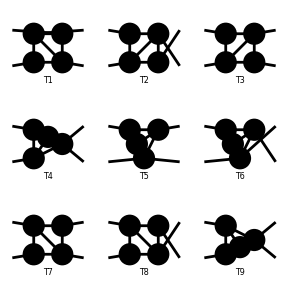

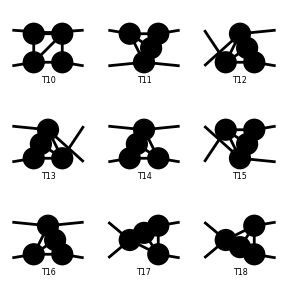

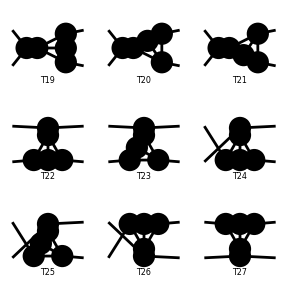

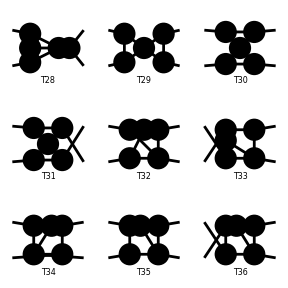

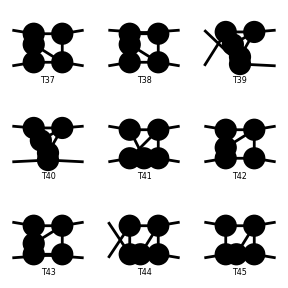

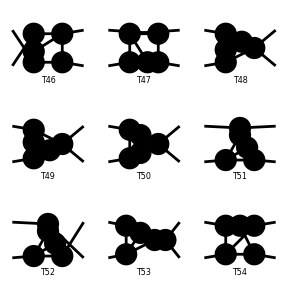

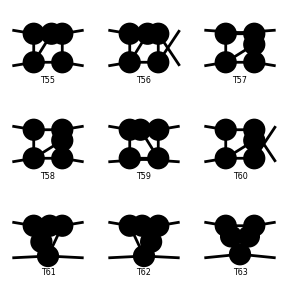

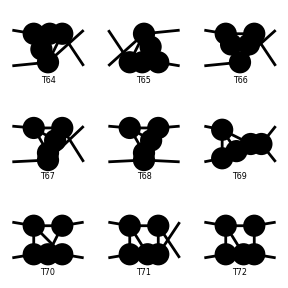

Number of topologies: 640

```mathematica
Paint[topologies2LCheck];
Print["Number of topologies: ",topologies2LCheck//Length]
```

#### Filtered

> Top. 1 aebe/cfdg/e12f2g21f1g1.m, 0 diagrams

> Top. 2 aebe/cfd1/eg2f2g21f1g1.m, 0 diagrams

> Top. 3 VFlip[aebe/cfd1/eg2f2g21f1g1.m], 0 diagrams

> Top. 4 aebe/cfdg/eh1f1g212f2hgh.m, 0 diagrams

> Top. 5 aebe/cfdg/ehfg1f1h212g2h.m, 0 diagrams

> Top. 6 aebe/cfdg/ehfh1f1g212g2h.m, 0 diagrams

> Top. 7 aebe/cfd1/e2f2f12121.m, 0 diagrams

> Top. 8 aebe/cfdg/egfgfhghhh.m, 0 diagrams

> Top. 9 VFlip[aebe/cfd1/e2f2f12121.m], 0 diagrams

> Top. 10 aebe/c1d2/eff2f12121.m, 0 diagrams

> Top. 11 aebe/c1df/ef21212f1f.m, 0 diagrams

> Top. 12 VFlip[aebe/cfdg/egfgfhghhh.m], 0 diagrams

> Top. 13 VFlip[aebe/c1df/ef21212f1f.m], 0 diagrams

> Top. 14 aebe/cfdf/eggfghfhhh.m, 0 diagrams

> Top. 15 aebe/cfdf/e121212f1f.m, 0 diagrams

> Top. 16 aebe/cfdg/ehfgfhgihiii.m, 0 diagrams

> Top. 17 VFlip[aebe/cfdg/ehfgfhgihiii.m], 0 diagrams

> Top. 18 aebe/cfdg/ehfgfigihihi.m, 0 diagrams

> Top. 19 aebe/cfdg/ehfhfighgiii.m, 0 diagrams

> Top. 20 aebe/cfdg/ehfhfigigihi.m, 0 diagrams

> Top. 21 VFlip[aebe/cfdg/ehfhfigigihi.m], 0 diagrams

> Top. 22 aebe/cfdg/e1fg2f2121g1.m, 0 diagrams

> Top. 23 VFlip[aebe/cfdg/e1fg2f2121g1.m], 0 diagrams

> Top. 24 aebe/cfd1/egfg2f2121g1.m, 0 diagrams

> Top. 25 aebe/cfd1/egfgf12g2121.m, 0 diagrams

> Top. 26 aebe/cfdg/eg1f21212gfg.m, 0 diagrams

> Top. 27 aebe/cfdg/eg1f212f2g1g.m, 0 diagrams

> Top. 28 VFlip[aebe/cfd1/egfg2f2121g1.m], 0 diagrams

> Top. 29 VFlip[aebe/cfd1/egfgf12g2121.m], 0 diagrams

> Top. 30 VFlip[aebe/cfdg/eg1f21212gfg.m], 0 diagrams

> Top. 31 VFlip[aebe/cfdg/eg1f212f2g1g.m], 0 diagrams

> Top. 32 aebe/cfdf/eg1g21212fgf.m, 0 diagrams

> Top. 33 aebe/cfdf/eg1g212g2f1f.m, 0 diagrams

> Top. 34 aebe/cfdg/eh1f1g1h2f2g2h.m, 0 diagrams

> Top. 35 aebe/cfdg/ehfg1f21212hgh.m, 0 diagrams

> Top. 36 VFlip[aebe/cfdg/ehfg1f21212hgh.m], 0 diagrams

> Top. 37 aebe/cfdg/ehfh1f21212ggh.m, 0 diagrams

> Top. 38 aebe/cfdg/egfhfhghgh.m, 0 diagrams

> Top. 39 VFlip[aebe/cfdg/egfhfhghgh.m], 0 diagrams

> Top. 40 aebe/cfdf/egghghfhfh.m, 0 diagrams

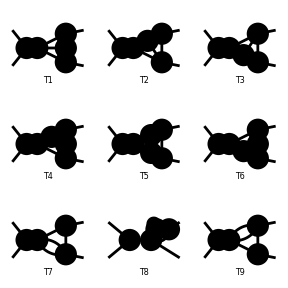

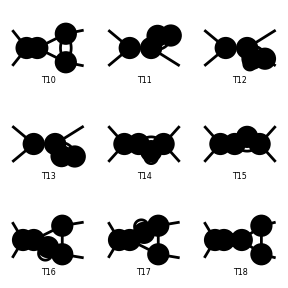

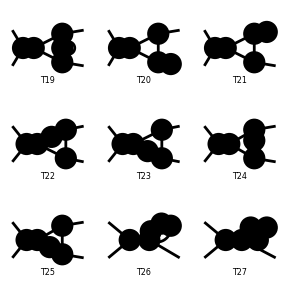

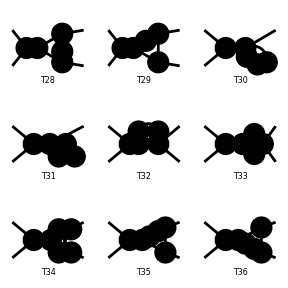

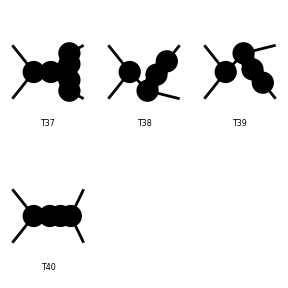

Number of topologies: 40

```mathematica
Paint[topologies2L];
Print["Number of topologies: ",topologies2L//Length]
```

```mathematica
Paint[topologies2LBX];
Paint[topologies2LTR];
Paint[topologies2LSE];
Paint[topologies2LTP];
Print["Number of topologies: ",topologies2L//Length]
Print["Boxes: ", Length[topologies2LBX],"  Triangles: ", Length[topologies2LTR],"  Selfe-Energies: ", Length[topologies2LSE],"  Tadpoles: ", Length[topologies2LTP]]
```

> Top. 1 aebe/cfdg/e12f2g21f1g1.m, 0 diagrams

> Top. 2 aebe/cfd1/eg2f2g21f1g1.m, 0 diagrams

> Top. 3 VFlip[aebe/cfd1/eg2f2g21f1g1.m], 0 diagrams

> Top. 4 aebe/cfdg/eh1f1g212f2hgh.m, 0 diagrams

> Top. 5 aebe/cfdg/ehfg1f1h212g2h.m, 0 diagrams

> Top. 6 aebe/cfdg/ehfh1f1g212g2h.m, 0 diagrams

> Top. 7 aebe/cfd1/e2f2f12121.m, 0 diagrams

> Top. 8 aebe/cfdg/egfgfhghhh.m, 0 diagrams

> Top. 9 VFlip[aebe/cfd1/e2f2f12121.m], 0 diagrams

> Top. 10 aebe/c1d2/eff2f12121.m, 0 diagrams

> Top. 11 aebe/c1df/ef21212f1f.m, 0 diagrams

> Top. 12 VFlip[aebe/cfdg/egfgfhghhh.m], 0 diagrams

> Top. 13 VFlip[aebe/c1df/ef21212f1f.m], 0 diagrams

> Top. 14 aebe/cfdf/eggfghfhhh.m, 0 diagrams

> Top. 15 aebe/cfdf/e121212f1f.m, 0 diagrams

> Top. 16 aebe/cfdg/ehfgfhgihiii.m, 0 diagrams

> Top. 17 VFlip[aebe/cfdg/ehfgfhgihiii.m], 0 diagrams

> Top. 18 aebe/cfdg/ehfgfigihihi.m, 0 diagrams

> Top. 19 aebe/cfdg/ehfhfighgiii.m, 0 diagrams

> Top. 20 aebe/cfdg/ehfhfigigihi.m, 0 diagrams

> Top. 21 VFlip[aebe/cfdg/ehfhfigigihi.m], 0 diagrams

> Top. 22 aebe/cfdg/e1fg2f2121g1.m, 0 diagrams

> Top. 23 VFlip[aebe/cfdg/e1fg2f2121g1.m], 0 diagrams

> Top. 24 aebe/cfd1/egfg2f2121g1.m, 0 diagrams

> Top. 25 aebe/cfd1/egfgf12g2121.m, 0 diagrams

> Top. 26 aebe/cfdg/eg1f21212gfg.m, 0 diagrams

> Top. 27 aebe/cfdg/eg1f212f2g1g.m, 0 diagrams

> Top. 28 VFlip[aebe/cfd1/egfg2f2121g1.m], 0 diagrams

> Top. 29 VFlip[aebe/cfd1/egfgf12g2121.m], 0 diagrams

> Top. 30 VFlip[aebe/cfdg/eg1f21212gfg.m], 0 diagrams

> Top. 31 VFlip[aebe/cfdg/eg1f212f2g1g.m], 0 diagrams

> Top. 32 aebe/cfdf/eg1g21212fgf.m, 0 diagrams

> Top. 33 aebe/cfdf/eg1g212g2f1f.m, 0 diagrams

> Top. 34 aebe/cfdg/eh1f1g1h2f2g2h.m, 0 diagrams

> Top. 35 aebe/cfdg/ehfg1f21212hgh.m, 0 diagrams

> Top. 36 VFlip[aebe/cfdg/ehfg1f21212hgh.m], 0 diagrams

> Top. 37 aebe/cfdg/ehfh1f21212ggh.m, 0 diagrams

> Top. 38 aebe/cfdg/egfhfhghgh.m, 0 diagrams

> Top. 39 VFlip[aebe/cfdg/egfhfhghgh.m], 0 diagrams

> Top. 40 aebe/cfdf/egghghfhfh.m, 0 diagrams

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Number of topologies: 40

Boxes: 0  Triangles: 40  Selfe-Energies: 0  Tadpoles: 0

## Select Topologies

> Top. 1 aebe/cfdg/e12f2g21f1g1.m, 0 diagrams

> Top. 2 aebe/cfd1/eg2f2g21f1g1.m, 0 diagrams

> Top. 3 VFlip[aebe/cfd1/eg2f2g21f1g1.m], 0 diagrams

> Top. 4 aebe/cfdg/eh1f1g212f2hgh.m, 0 diagrams

> Top. 5 aebe/cfdg/ehfg1f1h212g2h.m, 0 diagrams

> Top. 6 aebe/cfdg/ehfh1f1g212g2h.m, 0 diagrams

> Top. 7 aebe/cfd1/e2f2f12121.m, 0 diagrams

> Top. 8 aebe/cfdg/egfgfhghhh.m, 0 diagrams

> Top. 9 VFlip[aebe/cfd1/e2f2f12121.m], 0 diagrams

> Top. 10 aebe/c1d2/eff2f12121.m, 0 diagrams

> Top. 11 aebe/c1df/ef21212f1f.m, 0 diagrams

> Top. 12 VFlip[aebe/cfdg/egfgfhghhh.m], 0 diagrams

> Top. 13 VFlip[aebe/c1df/ef21212f1f.m], 0 diagrams

> Top. 14 aebe/cfdf/eggfghfhhh.m, 0 diagrams

> Top. 15 aebe/cfdf/e121212f1f.m, 0 diagrams

> Top. 16 aebe/cfdg/ehfgfhgihiii.m, 0 diagrams

> Top. 17 VFlip[aebe/cfdg/ehfgfhgihiii.m], 0 diagrams

> Top. 18 aebe/cfdg/ehfgfigihihi.m, 0 diagrams

> Top. 19 aebe/cfdg/ehfhfighgiii.m, 0 diagrams

> Top. 20 aebe/cfdg/ehfhfigigihi.m, 0 diagrams

> Top. 21 VFlip[aebe/cfdg/ehfhfigigihi.m], 0 diagrams

> Top. 22 aebe/cfdg/e1fg2f2121g1.m, 0 diagrams

> Top. 23 VFlip[aebe/cfdg/e1fg2f2121g1.m], 0 diagrams

> Top. 24 aebe/cfd1/egfg2f2121g1.m, 0 diagrams

> Top. 25 aebe/cfd1/egfgf12g2121.m, 0 diagrams

> Top. 26 aebe/cfdg/eg1f21212gfg.m, 0 diagrams

> Top. 27 aebe/cfdg/eg1f212f2g1g.m, 0 diagrams

> Top. 28 VFlip[aebe/cfd1/egfg2f2121g1.m], 0 diagrams

> Top. 29 VFlip[aebe/cfd1/egfgf12g2121.m], 0 diagrams

> Top. 30 VFlip[aebe/cfdg/eg1f21212gfg.m], 0 diagrams

> Top. 31 VFlip[aebe/cfdg/eg1f212f2g1g.m], 0 diagrams

> Top. 32 aebe/cfdf/eg1g21212fgf.m, 0 diagrams

> Top. 33 aebe/cfdf/eg1g212g2f1f.m, 0 diagrams

> Top. 34 aebe/cfdg/eh1f1g1h2f2g2h.m, 0 diagrams

> Top. 35 aebe/cfdg/ehfg1f21212hgh.m, 0 diagrams

> Top. 36 VFlip[aebe/cfdg/ehfg1f21212hgh.m], 0 diagrams

> Top. 37 aebe/cfdg/ehfh1f21212ggh.m, 0 diagrams

> Top. 38 aebe/cfdg/egfhfhghgh.m, 0 diagrams

> Top. 39 VFlip[aebe/cfdg/egfhfhghgh.m], 0 diagrams

> Top. 40 aebe/cfdf/egghghfhfh.m, 0 diagrams

-Graphics-

-Graphics-

-Graphics-

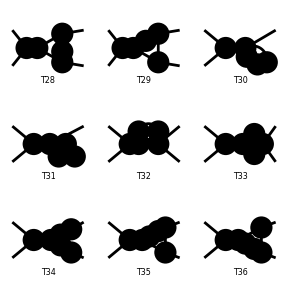

-Graphics-

```mathematica
Paint[topologies2L];
```

> Top. 1 aebe/cfdg/e12f2g21f1g1.m, 0 diagrams

> Top. 2 aebe/cfd1/eg2f2g21f1g1.m, 0 diagrams

> Top. 3 VFlip[aebe/cfd1/eg2f2g21f1g1.m], 0 diagrams

> Top. 4 aebe/cfdg/eh1f1g212f2hgh.m, 0 diagrams

> Top. 5 aebe/cfdg/ehfh1f1g212g2h.m, 0 diagrams

> Top. 6 aebe/cfd1/e2f2f12121.m, 0 diagrams

> Top. 7 aebe/cfdg/egfgfhghhh.m, 0 diagrams

> Top. 8 VFlip[aebe/cfd1/e2f2f12121.m], 0 diagrams

> Top. 9 aebe/c1d2/eff2f12121.m, 0 diagrams

> Top. 10 aebe/c1df/ef21212f1f.m, 0 diagrams

> Top. 11 VFlip[aebe/cfdg/egfgfhghhh.m], 0 diagrams

> Top. 12 VFlip[aebe/c1df/ef21212f1f.m], 0 diagrams

> Top. 13 aebe/cfdf/eggfghfhhh.m, 0 diagrams

> Top. 14 aebe/cfdf/e121212f1f.m, 0 diagrams

> Top. 15 aebe/cfdg/ehfgfhgihiii.m, 0 diagrams

> Top. 16 VFlip[aebe/cfdg/ehfgfhgihiii.m], 0 diagrams

> Top. 17 aebe/cfdg/ehfgfigihihi.m, 0 diagrams

> Top. 18 aebe/cfdg/ehfhfighgiii.m, 0 diagrams

> Top. 19 aebe/cfdg/ehfhfigigihi.m, 0 diagrams

> Top. 20 VFlip[aebe/cfdg/ehfhfigigihi.m], 0 diagrams

> Top. 21 aebe/cfdg/e1fg2f2121g1.m, 0 diagrams

> Top. 22 VFlip[aebe/cfdg/e1fg2f2121g1.m], 0 diagrams

> Top. 23 aebe/cfd1/egfg2f2121g1.m, 0 diagrams

> Top. 24 aebe/cfd1/egfgf12g2121.m, 0 diagrams

> Top. 25 aebe/cfdg/eg1f21212gfg.m, 0 diagrams

> Top. 26 aebe/cfdg/eg1f212f2g1g.m, 0 diagrams

> Top. 27 VFlip[aebe/cfd1/egfg2f2121g1.m], 0 diagrams

> Top. 28 VFlip[aebe/cfd1/egfgf12g2121.m], 0 diagrams

> Top. 29 VFlip[aebe/cfdg/eg1f21212gfg.m], 0 diagrams

> Top. 30 VFlip[aebe/cfdg/eg1f212f2g1g.m], 0 diagrams

> Top. 31 aebe/cfdf/eg1g21212fgf.m, 0 diagrams

> Top. 32 aebe/cfdf/eg1g212g2f1f.m, 0 diagrams

> Top. 33 aebe/cfdg/ehfg1f21212hgh.m, 0 diagrams

> Top. 34 VFlip[aebe/cfdg/ehfg1f21212hgh.m], 0 diagrams

> Top. 35 aebe/cfdg/ehfh1f21212ggh.m, 0 diagrams

> Top. 36 aebe/cfdg/egfhfhghgh.m, 0 diagrams

> Top. 37 VFlip[aebe/cfdg/egfhfhghgh.m], 0 diagrams

> Top. 38 aebe/cfdf/egghghfhfh.m, 0 diagrams

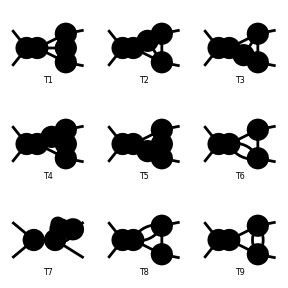

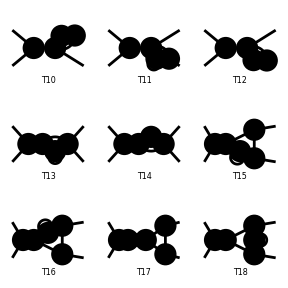

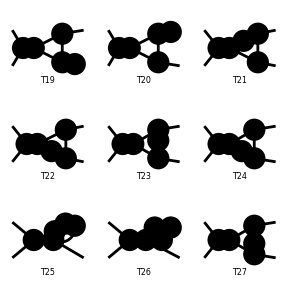

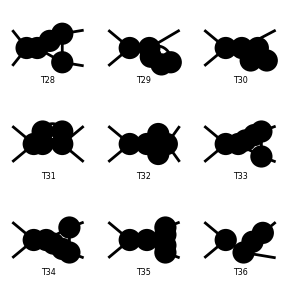

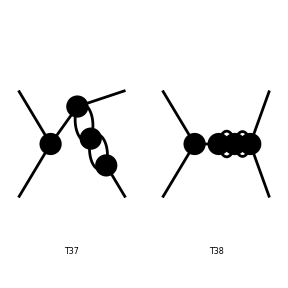

FeynArtsGraphics[2→2][([T1] | [T2] | [T3]
[T4] | [T5] | [T6]
[T7] | [T8] | [T9]),([T10] | [T11] | [T12]
[T13] | [T14] | [T15]
[T16] | [T17] | [T18]),([T19] | [T20] | [T21]
[T22] | [T23] | [T24]
[T25] | [T26] | [T27]),([T28] | [T29] | [T30]
[T31] | [T32] | [T33]
[T34] | [T35] | [T36]),([T37] | [T38] | Null
Null | Null | Null
Null | Null | Null)]

```mathematica
(*topologies2Lnoplanar=DiagramDelete[topologies2L,34];
topologies2Lnoplanar=DiagramDelete[topologies2Lnoplanar,5];*)
Paint[topologies2Lnoplanar]
```

## Insert Fields

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
```

### Born

```mathematica
fieldsBorn=InsertFields[topologiesBorn, process];
fieldsBorn=DiagramSelect[fieldsBorn,!FreeQ[#,Field[5]->V[10]]&];
Print["Number of diagrams: ",fieldsBorn//Length]
```

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 4 Particles insertions

Restoring 24 field point(s)

in total: 4 Particles insertions

Number of diagrams: 1

#### Paint

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

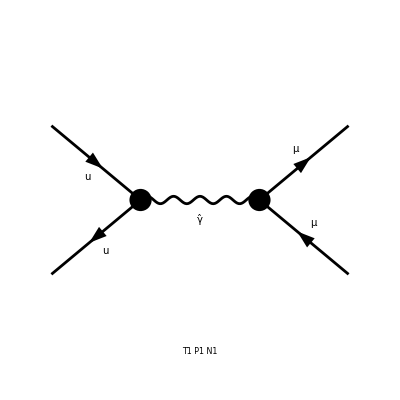

```mathematica
Paint[fieldsBorn];
```

### 1-Loop

```mathematica
fields1L=InsertFields[topologies1L, process];
fields1L=DiagramSelect[fields1L,!FreeQ[#,Field[5]->V[10]]&];
```

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 43 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 24 field point(s)

in total: 43 Particles insertions

#### Paint

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

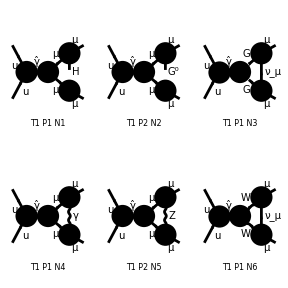

```mathematica
Paint[fields1L];
```

### 2-Loop

```mathematica
fields2L=InsertFields[topologies2L, process];
fields2L=DiagramSelect[fields2L,!FreeQ[#,Field[5]->V[10]]&];
```

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 84 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 481 Particles insertions

> Top. 5: 2667 Particles insertions

> Top. 6: 481 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 141 Particles insertions

> Top. 17: 141 Particles insertions

> Top. 18: 132 Particles insertions

> Top. 19: 92 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 250 Particles insertions

> Top. 23: 250 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 0 Particles insertions

> Top. 26: 0 Particles insertions

> Top. 27: 0 Particles insertions

> Top. 28: 0 Particles insertions

> Top. 29: 0 Particles insertions

> Top. 30: 0 Particles insertions

> Top. 31: 0 Particles insertions

> Top. 32: 0 Particles insertions

> Top. 33: 0 Particles insertions

> Top. 34: 307 Particles insertions

> Top. 35: 1273 Particles insertions

> Top. 36: 1273 Particles insertions

> Top. 37: 1144 Particles insertions

> Top. 38: 0 Particles insertions

> Top. 39: 0 Particles insertions

> Top. 40: 0 Particles insertions

Restoring 24 field point(s)

in total: 8716 Particles insertions

#### Paint

```mathematica
Paint[fields2L];
```

## Diagram Backup

## Save

```mathematica
fieldsBorn>>(NotebookDirectory[]<>"backup/fields/fieldsBorn.m");
fields1L>>(NotebookDirectory[]<>"backup/fields/fields1L.m");
fields2L>>(NotebookDirectory[]<>"backup/fields/fields2L.m");
```

## Load

```mathematica
fieldsBorn=<<(NotebookDirectory[]<>"backup/fields/fieldsBorn.m");
fields1L=<<(NotebookDirectory[]<>"backup/fields/fields1L.m");
fields2L=<<(NotebookDirectory[]<>"backup/fields/fields2L.m");
```

## Diagram Selection

We want to replicate the selection given by the QEDOnly option of FeynArts. We implement this with the use of DIagramSelect.

```mathematica
(* QEDOnly=ExcludeParticles->{F[1],V[2],V[3],S,SV,U[2],U[3],U[4]} *)
(* QEDOnly as defined in SM.mod *)
```

```mathematica
qedCondition=
(FreeQ[#,F[1,n___]]&&
FreeQ[#,V[2]]&&
FreeQ[#,V[3]]&&
FreeQ[#,S[n_]]&&
FreeQ[#,SV[n_]]&&
FreeQ[#,U[2]]&&
FreeQ[#,U[3]]&&
FreeQ[#,U[4]]&&
FreeQ[#,V[20]]&&
FreeQ[#,V[30]])&;
```

## Selection

```mathematica
(*fieldsBornQED=DiagramSelect[fieldsBorn,qedCondition];
fields1LQED=DiagramSelect[fields1L,qedCondition];
fields2LQED=DiagramSelect[fields2L,qedCondition];*)
```

```mathematica
fieldsBornnoT=deleteFermionTriangles[fieldsBorn];
fields1LnoT=deleteFermionTriangles[fields1L];
(*fields2LnoT=deleteFermionTriangles[fields2L];*)
```

```mathematica
fieldsBornnoT>>(NotebookDirectory[]<>"backup/fields/fieldsBornnoT.m");
fields1LnoT>>(NotebookDirectory[]<>"backup/fields/fields1LnoT.m");
(*fields2LnoT>>(NotebookDirectory[]<>"backup/fields/fields2LnoT.m");*)
```

### Born

```mathematica
fieldsBornQED=DiagramSelect[fieldsBorn,qedCondition];
```

#### Paint

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

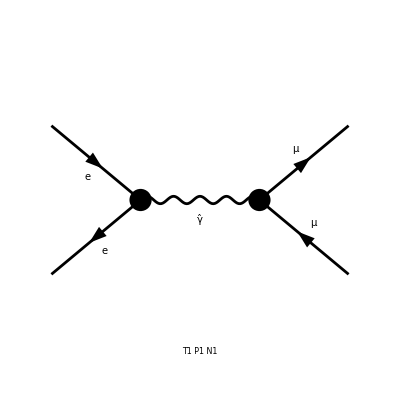

```mathematica
Paint[fieldsBornQEDnoT];
```

### 1-Loop

```mathematica
fields1LQED=DiagramSelect[fields1L,qedCondition];
```

#### Paint

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

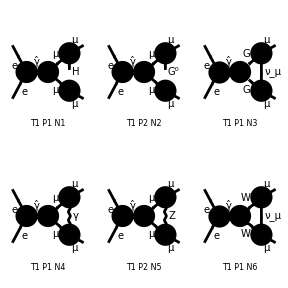

```mathematica
Paint[fields1L];
```

### 2-Loop

```mathematica
fields2LQED=DiagramSelect[fields2L,qedCondition];
```

#### Paint

```mathematica
Paint[fields2LnoT];
```

## Projection

## Amplitudes

### Paint

```mathematica
Paint[fields1LnoT];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 344 counterterms of order 1

> 26 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

-Graphics-

### Computation

```mathematica
ampBorn=CreateFeynAmp[fieldsBornnoT(*,GaugeRules->{}*)];
amp1L=CreateFeynAmp[fields1LnoT(*,GaugeRules->{}*)];
(*amp2L=CreateFeynAmp[fields2LnoT(*,GaugeRules->{}*)];*)
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 344 counterterms of order 1

> 26 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

creating amplitudes at level(s) {Particles}

> Top. 1: 6 Particles amplitudes

in total: 6 Particles amplitudes

```mathematica
myAmpBorn=ExtractAmplitude[ampBorn];
myAmp1L=ExtractAmplitude[amp1L];
(*myAmp2L=ExtractAmplitude[amp2L];*)
Print["Born: ", Length[myAmpBorn]]
Print["1L: ", Length[myAmp1L]]
(*Print[ "2L: ", Length[myAmp2L]]*)
```

Born: 1

1L: 6

```mathematica
SaveAmplitudes[myAmpBorn,OutputName->"BornAmplitudes.m"];
```

ABISS: Amplitudes saved in /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/feynArts_amplitudes/BornAmplitudes.m

```mathematica
SaveAmplitudes[myAmp1L,OutputName->"OneLoopAmplitudes.m"];
```

ABISS: Amplitudes saved in /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/feynArts_amplitudes/OneLoopAmplitudes.m

```mathematica
SaveAmplitudes[myAmp2L,OutputName->"TwoLoopAmplitudes.m"];
```

ABISS: Amplitudes saved in /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/feynArts_amplitudes/TwoLoopAmplitudes.m

## Amplitude Backup

```mathematica
myAmpBorn=<<(NotebookDirectory[]<>"feynArts_amplitudes/BornAmplitudes.m");
myAmp1L=<<(NotebookDirectory[]<>"feynArts_amplitudes/OneLoopAmplitudes.m");
(*myAmp2L=<<(NotebookDirectory[]<>"feynArts_amplitudes/TwoLoopAmplitudes.m");*)
Print["Number of diagrams: ", {myAmpBorn,myAmp1L(*,myAmp2L*)}//Map[Length]]
```

Number of diagrams: {1,6}

## Interference

### Mass Options

```mathematica
normalMass={};
SetZeroMassParticles[normalMass]
```

```mathematica
zeroMass={mu->0,md->0,ms->0,me->0(*,mm->0*)};
SetZeroMassParticles[zeroMass]
```

```mathematica
(*myAmpBorn=myAmpBorn/.zeroOnShellMass;
myAmp1L=myAmp1L/.zeroOnShellMass;*)
```

### Computation

```mathematica
ImportInput[]
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/input/equivalence_classes.m

We want an estimate of the computational time

```mathematica
noInP={
FermionChain[NonCommutative[DiracSpinor[-FourMomentum[Incoming, 2], MU]], I*EL*gAu*NonCommutative[DiracMatrix[Index[Lorentz, 1]], ChiralityProjector[-1]]+ 
   I*EL*gAu*NonCommutative[DiracMatrix[Index[Lorentz, 1]], ChiralityProjector[1]], NonCommutative[DiracSpinor[FourMomentum[Incoming, 1], MU]]]->1,
MetricTensor[Index[Lorentz,1],Index[Lorentz,2]]->1,
PropagatorDenominator[FourMomentum[Outgoing,1]+FourMomentum[Outgoing,2],0]->1
}
```

{DiracSpinor[-(p2),MU].(ⅈ EL gAu DiracMatrix[Lor1].ChiralityProjector[-1]+ⅈ EL gAu DiracMatrix[Lor1].ChiralityProjector[1]).DiracSpinor[p1,MU]→1,MetricTensor[Lor1,Lor2]→1,1/(k1+k2)^2→1}

```mathematica
inMom=FourVector[FourMomentum[Incoming,1]+FourMomentum[Incoming,2],Index[Lorentz,2]]
```

FourVector[p1+p2,Lor2]

```mathematica
proj=FermionChain[NonCommutative[DiracSpinor[FourMomentum[Outgoing,1],MM]],EL*NonCommutative[ChiralityProjector[1]]+EL*NonCommutative[ChiralityProjector[-1]],NonCommutative[DiracSpinor[-FourMomentum[Outgoing,2],MM]]]/EL
```

(DiracSpinor[k1,MM].(EL ChiralityProjector[-1]+EL ChiralityProjector[1]).DiracSpinor[-(k2),MM])/EL

```mathematica
projN=
 FermionChain[NonCommutative[DiracSpinor[FourMomentum[Outgoing, 1], MM]],EL*NonCommutative[DiracSlash[n]],NonCommutative[DiracSpinor[-FourMomentum[Outgoing, 2], MM]]]/EL
```

(DiracSpinor[k1,MM].(EL DiracSlash[n]).DiracSpinor[-(k2),MM])/EL

```mathematica
projP=
 FermionChain[NonCommutative[DiracSpinor[FourMomentum[Outgoing, 1], MM]],
 aa*EL*NonCommutative[DiracSlash[p1]]+bb*EL*NonCommutative[DiracSlash[p2]](*+cc*EL*NonCommutative[DiracSlash[p3]]*),
 NonCommutative[DiracSpinor[-FourMomentum[Outgoing, 2], MM]]]/EL
```

(DiracSpinor[k1,MM].(aa EL DiracSlash[p1]+bb EL DiracSlash[p2]).DiracSpinor[-(k2),MM])/EL

```mathematica
AmpSquare[projN,projN]
AmpSquare[projN,proj]
AmpSquare[proj,proj]
AmpSquare[projP,projP]/.bb->aa//Simplify
AmpSquare[inMom*(myAmpBorn/.noInP),projN]
```

1/4 (-2 (2 mm^2-2 psq+s) SP[n,n]+8 (SP[n,p1]+SP[n,p2]-SP[n,p3]) SP[n,p3])

mm (SP[n,p1]+SP[n,p2]-2 SP[n,p3])

1/4 (-4 mm^2-4 psq+2 s)

aa^2 (-mm^2+psq) s

{-ⅈ EL gAl (mm^2-psq) (SP[n,p1]+SP[n,p2])}

```mathematica
SquareAndSave[inMom*(myAmp1L/.noInP),{projP}]
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/interferences/Contribution_1_1.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/interferences/Contribution_2_1.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/interferences/Contribution_3_1.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/interferences/Contribution_4_1.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/interferences/Contribution_5_1.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/interferences/Contribution_6_1.m.

## Shift

## Squared Matrix Element Backup

```mathematica
sm=Table[<<(NotebookDirectory[]<>"interferences/Contribution_"<>ToString[i]<>"_1.m"),{i,6}];
Length[sm]
```

6

```mathematica
sm//Variables
```

{aa,bb,d,EL,gAl,gFFA,gFll,gHll,gWlN,gWNl,gWWA,gXll,gZlL,gZlR,mm,psq,s,t,μ,μ^d,PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mm],KiraPropagator[-p1-p2+p3+q1,mm]],PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw]],PropList[KiraPropagator[q1,mh],KiraPropagator[p3+q1,mm],KiraPropagator[-p1-p2+p3+q1,mm]],PropList[KiraPropagator[q1,mz],KiraPropagator[p3+q1,mm],KiraPropagator[-p1-p2+p3+q1,mm]],SPList[SP[p1,q1]],SPList[SP[p2,q1]],SPList[SP[p3,q1]],SPList[SP[q1,q1]],SPList[SP[p1,q1],SP[p1,q1]],SPList[SP[p1,q1],SP[p2,q1]],SPList[SP[p1,q1],SP[p3,q1]],SPList[SP[p2,q1],SP[p2,q1]],SPList[SP[p2,q1],SP[p3,q1]]}

```mathematica
Do[
Print[i];
smi =sm[[i]]/.ShiftToIntegralFamily[sm[[i]]];
smi>>(NotebookDirectory[]<>"interferences/Contribution_"<>ToString[i]<>"_1.m")
,{i,Length[sm]}]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

201

202

203

204

205

206

207

208

209

210

211

212

213

214

215

216

217

218

219

220

221

222

223

224

225

226

227

228

229

230

231

232

233

234

235

236

237

238

239

240

241

242

243

244

245

246

247

248

249

250

251

252

253

254

255

256

257

258

259

260

261

262

263

264

265

266

267

268

269

270

271

272

273

274

275

276

277

278

## Shift and Save

```mathematica
ImportInput[]
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/input/equivalence_classes.m

```mathematica
l=6;
ExtractFamily[sm[[l]]/.ShiftToIntegralFamily[sm[[l]]]]
ShiftToIntegralFamily[sm[[l]]]
extractKiraProp[sm[[l]]]
extractMomenta[sm[[l]]]
```

{A3,{mw}}

{{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1}}

KiraPropagator[q1,0] KiraPropagator[p3+q1,mw] KiraPropagator[-p1-p2+p3+q1,mw]

{q1,p3+q1,-p1-p2+p3+q1}

```mathematica
Do[
Print[i, "  ",ShiftToIntegralFamily[sm[[i]]]]
,{i,1,6}]
```

6  {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1}}

5  {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1}}

4  {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1}}

3  {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1}}

2  {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1}}

1  {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1}}

```mathematica
Cases[sm,PropList[___],Infinity]
```

{PropList[KiraPropagator[q1,mh],KiraPropagator[p3+q1,mm],KiraPropagator[-p1-p2+p3+q1,mm]],PropList[KiraPropagator[q1,mz],KiraPropagator[p3+q1,mm],KiraPropagator[-p1-p2+p3+q1,mm]],PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw]],PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mm],KiraPropagator[-p1-p2+p3+q1,mm]],PropList[KiraPropagator[q1,mz],KiraPropagator[p3+q1,mm],KiraPropagator[-p1-p2+p3+q1,mm]],PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw]]}

```mathematica
Do[
ShiftAndSave[i,j];
,{i,1,6},{j,1}]
```

ABISS: Integral family {{A4, {mh, mm}}} recognised for /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/interferences/Contribution_1_1.m.

ABISS: Integral family {{A4, {mz, mm}}} recognised for /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/interferences/Contribution_2_1.m.

ABISS: Integral family {{A3, {mw}}} recognised for /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/interferences/Contribution_3_1.m.

ABISS: Integral family {{A3, {mm}}} recognised for /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/interferences/Contribution_4_1.m.

ABISS: Integral family {{A4, {mz, mm}}} recognised for /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/interferences/Contribution_5_1.m.

ABISS: Integral family {{A3, {mw}}} recognised for /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/interferences/Contribution_6_1.m.

## Kira Input

```mathematica
ImportInput[]
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/input/equivalence_classes.m

```mathematica
Off[General::stop]
```

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,1,6},{j,1}]
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/kira_input/Contribution_1_1.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/kira_input/Contribution_2_1.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/kira_input/Contribution_3_1.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/kira_input/Contribution_4_1.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/kira_input/Contribution_5_1.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/kira_input/Contribution_6_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A4,{mh,mm},0,0,1,0],userIntegral[A4,{mh,mm},0,1,0,0],userIntegral[A4,{mh,mm},1,-1,1,0],userIntegral[A4,{mh,mm},1,0,0,0],userIntegral[A4,{mh,mm},1,0,1,-1],userIntegral[A4,{mh,mm},1,0,1,0],userIntegral[A4,{mh,mm},1,1,-1,0],userIntegral[A4,{mh,mm},1,1,0,-1],userIntegral[A4,{mh,mm},1,1,0,0],userIntegral[A4,{mz,mm},0,0,1,0],userIntegral[A4,{mz,mm},0,1,0,0],userIntegral[A4,{mz,mm},1,-1,1,0],userIntegral[A4,{mz,mm},1,0,0,0],userIntegral[A4,{mz,mm},1,0,1,-1],userIntegral[A4,{mz,mm},1,0,1,0],userIntegral[A4,{mz,mm},1,1,-1,0],userIntegral[A4,{mz,mm},1,1,0,-1],userIntegral[A4,{mz,mm},1,1,0,0],userIntegral[A3,{mw},0,0,1,0],userIntegral[A3,{mw},0,1,0,0],userIntegral[A3,{mw},1,-1,1,0],userIntegral[A3,{mw},1,0,0,0],userIntegral[A3,{mw},1,0,1,-1],userIntegral[A3,{mw},1,0,1,0],userIntegral[A3,{mw},1,1,-1,0],userIntegral[A3,{mw},1,1,0,-1],userIntegral[A3,{mw},1,1,0,0],userIntegral[A3,{mm},0,0,1,0],userIntegral[A3,{mm},0,1,0,0],userIntegral[A3,{mm},1,-1,1,0],userIntegral[A3,{mm},1,0,0,0],userIntegral[A3,{mm},1,0,1,-1],userIntegral[A3,{mm},1,0,1,0],userIntegral[A3,{mm},1,1,-1,0],userIntegral[A3,{mm},1,1,0,-1],userIntegral[A3,{mm},1,1,0,0]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Calcolo di r e s

```mathematica
si=<<(NotebookDirectory[]<>"scalar_integrals.m");
Length[si]
```

36

```mathematica
Print["r: ",findR[si]," s: ",findS[si]];
```

r: 2 s: 1

## Kira Input Backup

```mathematica
kin=Table[Simplify[<<(NotebookDirectory[]<>"kira_input/Contribution_"<>ToString[i]<>"_"<>ToString[j]<>".m")]
,{i,6},{j,1}];
```

```mathematica
(kin/.Pi->myPi//Simplify)/.myPi->Pi
```

{{2^(-2-d) EL^3 gAl gHll^2 mm^2 π^-d μ^(4-d) (2 (aa-bb) (mm^2-t) userIntegral[A4,{mh,mm},0,0,1,0]-2 (aa-bb) (mm^2-t) userIntegral[A4,{mh,mm},0,1,0,0]+(bb (psq-s-t)+aa (2 mm^2-3 psq+s+t)) userIntegral[A4,{mh,mm},1,-1,1,0]+(bb s-aa (4 mm^2-4 psq+s)) userIntegral[A4,{mh,mm},1,0,0,0]-(aa-bb) (2 mm^2-2 psq+s) userIntegral[A4,{mh,mm},1,0,1,-1]+(bb (psq s+mm^2 (8 psq-5 s-8 t)-2 mh^2 (mm^2-t))+aa (psq s+2 mh^2 (mm^2-t)+mm^2 (-8 psq+3 s+8 t))) userIntegral[A4,{mh,mm},1,0,1,0]+(aa (2 mm^2-psq-t)+bb (-psq+t)) userIntegral[A4,{mh,mm},1,1,-1,0]+(aa-bb) (2 mm^2-2 psq+s) userIntegral[A4,{mh,mm},1,1,0,-1]+(aa (psq s+mm^2 (8 psq-5 s-8 t)-2 mh^2 (mm^2-t))+bb (psq s+2 mh^2 (mm^2-t)+mm^2 (-8 psq+3 s+8 t))) userIntegral[A4,{mh,mm},1,1,0,0])},{2^(-2-d) EL^3 gAl gXll^2 mm^2 π^-d μ^(4-d) (2 (aa-bb) (mm^2-t) userIntegral[A4,{mz,mm},0,0,1,0]-2 (aa-bb) (mm^2-t) userIntegral[A4,{mz,mm},0,1,0,0]+(bb (psq-s-t)+aa (2 mm^2-3 psq+s+t)) userIntegral[A4,{mz,mm},1,-1,1,0]+(bb s-aa (4 mm^2-4 psq+s)) userIntegral[A4,{mz,mm},1,0,0,0]-(aa-bb) (2 mm^2-2 psq+s) userIntegral[A4,{mz,mm},1,0,1,-1]+(aa (mm^2 (2 mz^2-s)+psq s-2 mz^2 t)+bb (psq s-mm^2 (2 mz^2+s)+2 mz^2 t)) userIntegral[A4,{mz,mm},1,0,1,0]+(aa (2 mm^2-psq-t)+bb (-psq+t)) userIntegral[A4,{mz,mm},1,1,-1,0]+(aa-bb) (2 mm^2-2 psq+s) userIntegral[A4,{mz,mm},1,1,0,-1]+(bb (mm^2 (2 mz^2-s)+psq s-2 mz^2 t)+aa (psq s-mm^2 (2 mz^2+s)+2 mz^2 t)) userIntegral[A4,{mz,mm},1,1,0,0])},{2^(-3-d) EL^3 gFFA gFll^2 mm^2 π^-d μ^(4-d) (-2 (aa-bb) (mm^2-t) userIntegral[A3,{mw},0,0,1,0]+2 (aa-bb) (mm^2-t) userIntegral[A3,{mw},0,1,0,0]-(bb (psq-s-t)+aa (2 mm^2-3 psq+s+t)) userIntegral[A3,{mw},1,-1,1,0]+(-bb s+aa (4 mm^2-4 psq+s)) userIntegral[A3,{mw},1,0,0,0]+(aa-bb) (2 mm^2-2 psq+s) userIntegral[A3,{mw},1,0,1,-1]+(aa-bb) (mw^2-psq) (2 psq-s-2 t) userIntegral[A3,{mw},1,0,1,0]-(aa (2 mm^2-psq-t)+bb (-psq+t)) userIntegral[A3,{mw},1,1,-1,0]-(aa-bb) (2 mm^2-2 psq+s) userIntegral[A3,{mw},1,1,0,-1]+(aa-bb) (-mw^2+psq) (2 psq-s-2 t) userIntegral[A3,{mw},1,1,0,0])},{2^(-2-d) EL^3 gAl^3 π^-d μ^(4-d) (2 (aa-bb) (-2+d) (mm^2-t) userIntegral[A3,{mm},0,0,1,0]-2 (aa-bb) (-2+d) (mm^2-t) userIntegral[A3,{mm},0,1,0,0]+(-2+d) (bb (psq-s-t)+aa (2 mm^2-3 psq+s+t)) userIntegral[A3,{mm},1,-1,1,0]+(-2+d) (bb s-aa (4 mm^2-4 psq+s)) userIntegral[A3,{mm},1,0,0,0]-(aa-bb) (-2+d) (2 mm^2-2 psq+s) userIntegral[A3,{mm},1,0,1,-1]+(aa (-2+d) psq s+bb (-2+d) psq s+aa mm^2 (8 psq-(2+d) s-8 t)+bb mm^2 (-8 psq-(-6+d) s+8 t)) userIntegral[A3,{mm},1,0,1,0]+(2-d) (bb (psq-t)+aa (-2 mm^2+psq+t)) userIntegral[A3,{mm},1,1,-1,0]+(aa-bb) (-2+d) (2 mm^2-2 psq+s) userIntegral[A3,{mm},1,1,0,-1]-(-aa (-2+d) psq s-bb (-2+d) psq s+aa mm^2 (8 psq+(-6+d) s-8 t)+bb mm^2 (-8 psq+(2+d) s+8 t)) userIntegral[A3,{mm},1,1,0,0])},{2^(-3-d) EL^3 gAl π^-d μ^(4-d) (2 (aa-bb) (-2+d) (gZlL^2+gZlR^2) (mm^2-t) userIntegral[A4,{mz,mm},0,0,1,0]-2 (aa-bb) (-2+d) (gZlL^2+gZlR^2) (mm^2-t) userIntegral[A4,{mz,mm},0,1,0,0]+(-2+d) (gZlL^2+gZlR^2) (bb (psq-s-t)+aa (2 mm^2-3 psq+s+t)) userIntegral[A4,{mz,mm},1,-1,1,0]+(-2+d) (gZlL^2+gZlR^2) (bb s-aa (4 mm^2-4 psq+s)) userIntegral[A4,{mz,mm},1,0,0,0]-(aa-bb) (-2+d) (gZlL^2+gZlR^2) (2 mm^2-2 psq+s) userIntegral[A4,{mz,mm},1,0,1,-1]+(aa (4 d gZlL gZlR mm^2 (2 psq-s-2 t)+(-2+d) gZlL^2 (psq s-2 mz^2 t+mm^2 (2 mz^2-4 psq+s+4 t))+(-2+d) gZlR^2 (psq s-2 mz^2 t+mm^2 (2 mz^2-4 psq+s+4 t)))+bb (4 d gZlL gZlR mm^2 (-2 psq+s+2 t)-(-2+d) gZlL^2 (-psq s-2 mz^2 t+mm^2 (2 mz^2-4 psq+3 s+4 t))-(-2+d) gZlR^2 (-psq s-2 mz^2 t+mm^2 (2 mz^2-4 psq+3 s+4 t)))) userIntegral[A4,{mz,mm},1,0,1,0]-(-2+d) (gZlL^2+gZlR^2) (bb (psq-t)+aa (-2 mm^2+psq+t)) userIntegral[A4,{mz,mm},1,1,-1,0]+(aa-bb) (-2+d) (gZlL^2+gZlR^2) (2 mm^2-2 psq+s) userIntegral[A4,{mz,mm},1,1,0,-1]+(bb (4 d gZlL gZlR mm^2 (2 psq-s-2 t)+(-2+d) gZlL^2 (psq s-2 mz^2 t+mm^2 (2 mz^2-4 psq+s+4 t))+(-2+d) gZlR^2 (psq s-2 mz^2 t+mm^2 (2 mz^2-4 psq+s+4 t)))+aa (4 d gZlL gZlR mm^2 (-2 psq+s+2 t)-(-2+d) gZlL^2 (-psq s-2 mz^2 t+mm^2 (2 mz^2-4 psq+3 s+4 t))-(-2+d) gZlR^2 (-psq s-2 mz^2 t+mm^2 (2 mz^2-4 psq+3 s+4 t)))) userIntegral[A4,{mz,mm},1,1,0,0])},{2^(-3-d) (-2+d) EL^3 gWlN gWNl gWWA π^-d μ^(4-d) (-2 (aa-bb) (mm^2-t) userIntegral[A3,{mw},0,0,1,0]+2 (aa-bb) (mm^2-t) userIntegral[A3,{mw},0,1,0,0]-(bb (psq-s-t)+aa (2 mm^2-3 psq+s+t)) userIntegral[A3,{mw},1,-1,1,0]+(-bb s+aa (4 mm^2-4 psq+s)) userIntegral[A3,{mw},1,0,0,0]+(aa-bb) (2 mm^2-2 psq+s) userIntegral[A3,{mw},1,0,1,-1]+(aa-bb) (mw^2-psq) (2 psq-s-2 t) userIntegral[A3,{mw},1,0,1,0]+(bb (psq-t)+aa (-2 mm^2+psq+t)) userIntegral[A3,{mw},1,1,-1,0]-(aa-bb) (2 mm^2-2 psq+s) userIntegral[A3,{mw},1,1,0,-1]+(aa-bb) (-mw^2+psq) (2 psq-s-2 t) userIntegral[A3,{mw},1,1,0,0])}}

## r and s for each family

```mathematica
Do[
sitmp=collectByIFname[si,userIntegralFamiliesNames[[i]]];
rtmp=findR[sitmp];
stmp=findS[sitmp];
Print[ToString[userIntegralFamiliesNames[[i]]],"  r: ",rtmp," s: ",stmp," sectors: ",findActiveSectors[sitmp],"  ", userIntegralMasses[userIntegralFamiliesNames[[i]]]]
,{i,Length[userIntegralFamiliesNames]}]
```

A1  r: -∞ s: -∞ sectors: {0,0,0,0,0,0,0,0,0}  {0,0,0,0}

A2  r: -∞ s: -∞ sectors: {0,0,0,0,0,0,0,0,0}  {M1,0,0,0}

A3  r: 2 s: 1 sectors: {1,1,1,0,0,0,0,0,0}  {0,M1,M1,0}

A4  r: 2 s: 1 sectors: {1,1,1,0,0,0,0,0,0}  {M1,M2,M2,0}

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A4,{mh,mm},0,0,1,0],userIntegral[A4,{mh,mm},0,1,0,0],userIntegral[A4,{mh,mm},1,-1,1,0],userIntegral[A4,{mh,mm},1,0,0,0],userIntegral[A4,{mh,mm},1,0,1,-1],userIntegral[A4,{mh,mm},1,0,1,0],userIntegral[A4,{mh,mm},1,1,-1,0],userIntegral[A4,{mh,mm},1,1,0,-1],userIntegral[A4,{mh,mm},1,1,0,0],userIntegral[A4,{mz,mm},0,0,1,0],userIntegral[A4,{mz,mm},0,1,0,0],userIntegral[A4,{mz,mm},1,-1,1,0],userIntegral[A4,{mz,mm},1,0,0,0],userIntegral[A4,{mz,mm},1,0,1,-1],userIntegral[A4,{mz,mm},1,0,1,0],userIntegral[A4,{mz,mm},1,1,-1,0],userIntegral[A4,{mz,mm},1,1,0,-1],userIntegral[A4,{mz,mm},1,1,0,0],userIntegral[A3,{mw},0,0,1,0],userIntegral[A3,{mw},0,1,0,0],userIntegral[A3,{mw},1,-1,1,0],userIntegral[A3,{mw},1,0,0,0],userIntegral[A3,{mw},1,0,1,-1],userIntegral[A3,{mw},1,0,1,0],userIntegral[A3,{mw},1,1,-1,0],userIntegral[A3,{mw},1,1,0,-1],userIntegral[A3,{mw},1,1,0,0],userIntegral[A3,{mm},0,0,1,0],userIntegral[A3,{mm},0,1,0,0],userIntegral[A3,{mm},1,-1,1,0],userIntegral[A3,{mm},1,0,0,0],userIntegral[A3,{mm},1,0,1,-1],userIntegral[A3,{mm},1,0,1,0],userIntegral[A3,{mm},1,1,-1,0],userIntegral[A3,{mm},1,1,0,-1],userIntegral[A3,{mm},1,1,0,0]}

```mathematica
GenerateKiraRun[]
```

ABISS: The kira runs have been generated in /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/kira_run/

```mathematica
ClearRules[]
```

{}

```mathematica
userIntegralFamiliesNames
```

{A1,A2,A3,A4}

```mathematica
ifnlist=Map[ToString,userIntegralFamiliesNames]
```

{A1,A2,A3,A4}

```mathematica
ifnlist=DeleteCases[ifnlist,"A1"]
ifnlist=DeleteCases[ifnlist,"A2"]
```

{A2,A3,A4}

{A3,A4}

```mathematica
ClearRules[]
Do[
ImportRules[NotebookDirectory[]<>"rules/"<>ToString[ifnlist[[i]]]<>"/kira_myintegrals.m"]
,{i,Length[ifnlist]}]
```

{}

```mathematica
ClearRules[]
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

{}

```mathematica
PrintRules[]
```

{userIntegral[A3,{m1},1,0,0,0]→0,userIntegral[A3,{m1},0,0,1,0]→userIntegral[A3,{m1},0,1,0,0],userIntegral[A3,{m1},1,-1,1,0]→(s userIntegral[A3,{m1},0,1,0,0])/(2 psq)+((-m1^2 s+psq s) userIntegral[A3,{m1},1,1,0,0])/(2 psq),userIntegral[A3,{m1},1,0,1,-1]→((psq+s+t) userIntegral[A3,{m1},0,1,0,0])/(2 psq)+((-psq^2+psq s+m1^2 (psq-s-t)+psq t) userIntegral[A3,{m1},1,1,0,0])/(2 psq),userIntegral[A3,{m1},1,0,1,0]→userIntegral[A3,{m1},1,1,0,0],userIntegral[A3,{m1},1,1,-1,0]→(s userIntegral[A3,{m1},0,1,0,0])/(2 psq)+((-m1^2 s+psq s) userIntegral[A3,{m1},1,1,0,0])/(2 psq),userIntegral[A3,{m1},1,1,0,-1]→((psq+t) userIntegral[A3,{m1},0,1,0,0])/(2 psq)+((-psq^2+m1^2 (psq-t)+psq t) userIntegral[A3,{m1},1,1,0,0])/(2 psq),userIntegral[A4,{m1,m2},0,0,1,0]→userIntegral[A4,{m1,m2},0,1,0,0],userIntegral[A4,{m1,m2},1,-1,1,0]→(s userIntegral[A4,{m1,m2},0,1,0,0])/(2 psq)+((2 psq-s) userIntegral[A4,{m1,m2},1,0,0,0])/(2 psq)+((m1^2 s-m2^2 s+psq s) userIntegral[A4,{m1,m2},1,1,0,0])/(2 psq),userIntegral[A4,{m1,m2},1,0,1,-1]→((psq+s+t) userIntegral[A4,{m1,m2},0,1,0,0])/(2 psq)+((psq-s-t) userIntegral[A4,{m1,m2},1,0,0,0])/(2 psq)+((-psq^2+psq s+m2^2 (psq-s-t)+psq t+m1^2 (psq+s+t)) userIntegral[A4,{m1,m2},1,1,0,0])/(2 psq),userIntegral[A4,{m1,m2},1,0,1,0]→userIntegral[A4,{m1,m2},1,1,0,0],userIntegral[A4,{m1,m2},1,1,-1,0]→(s userIntegral[A4,{m1,m2},0,1,0,0])/(2 psq)+((2 psq-s) userIntegral[A4,{m1,m2},1,0,0,0])/(2 psq)+((m1^2 s-m2^2 s+psq s) userIntegral[A4,{m1,m2},1,1,0,0])/(2 psq),userIntegral[A4,{m1,m2},1,1,0,-1]→((psq+t) userIntegral[A4,{m1,m2},0,1,0,0])/(2 psq)+((psq-t) userIntegral[A4,{m1,m2},1,0,0,0])/(2 psq)+((-psq^2+m2^2 (psq-t)+psq t+m1^2 (psq+t)) userIntegral[A4,{m1,m2},1,1,0,0])/(2 psq)}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[A4,{mh,mm},0,1,0,0],userIntegral[A4,{mh,mm},1,0,0,0],userIntegral[A4,{mh,mm},1,1,0,0],userIntegral[A4,{mz,mm},0,1,0,0],userIntegral[A4,{mz,mm},1,0,0,0],userIntegral[A4,{mz,mm},1,1,0,0],userIntegral[A3,{mw},0,1,0,0],userIntegral[A3,{mw},1,1,0,0],userIntegral[A3,{mm},0,1,0,0],userIntegral[A3,{mm},1,1,0,0]}

```mathematica
Do[
SaveResult[i,j];
,{i,1,6},{j,1}]
```

ABISS: Saved file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/coefficients/Masters.m

ABISS: Saved file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/coefficients/Coefficients_1_1.m

ABISS: Saved file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/coefficients/Coefficients_2_1.m

ABISS: Saved file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/coefficients/Coefficients_3_1.m

ABISS: Saved file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/coefficients/Coefficients_4_1.m

ABISS: Saved file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/coefficients/Coefficients_5_1.m

ABISS: Saved file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm1L_ward/coefficients/Coefficients_6_1.m

## Master reduction

```mathematica
masters=<<(NotebookDirectory[]<>"coefficients/Masters.m");
Length[masters]
```

10

## r and s calculation

```mathematica
Length[masters]
```

10

### Total

```mathematica
Print["Total masters  r: ",findR[masters]," s: ",findS[masters]]
```

Total masters  r: 2 s: 0

### Integral Families

```mathematica
Do[
sitmp=collectByIFname[si,userIntegralFamiliesNames[[i]]];
rtmp=findR[sitmp];
stmp=findS[sitmp];
Print[ToString[userIntegralFamiliesNames[[i]]],"  r: ",rtmp," s: ",stmp," sectors: ",findActiveSectors[sitmp],"  ", userIntegralMasses[userIntegralFamiliesNames[[i]]]]
,{i,Length[userIntegralFamiliesNames]}]
```

A1  r: -∞ s: -∞ sectors: {0,0,0,0,0,0,0,0,0}  {0,0,0,0}

A2  r: -∞ s: -∞ sectors: {0,0,0,0,0,0,0,0,0}  {M1,0,0,0}

A3  r: 2 s: 1 sectors: {1,1,1,0,0,0,0,0,0}  {0,M1,M1,0}

A4  r: 2 s: 1 sectors: {1,1,1,0,0,0,0,0,0}  {M1,M2,M2,0}

```mathematica
Do[
sitmp=collectByIFname[masters,userIntegralFamiliesNames[[i]]];
rtmp=findR[sitmp];
stmp=findS[sitmp];
Print[ToString[userIntegralFamiliesNames[[i]]],"  r: ",rtmp," s: ",stmp," sectors: ",findActiveSectors[sitmp],"  ", userIntegralMasses[userIntegralFamiliesNames[[i]]]]
,{i,Length[userIntegralFamiliesNames]}]
```

A1  r: -∞ s: -∞ sectors: {0,0,0,0,0,0,0,0,0}  {0,0,0,0}

A2  r: -∞ s: -∞ sectors: {0,0,0,0,0,0,0,0,0}  {M1,0,0,0}

A3  r: 2 s: 0 sectors: {1,1,0,0,0,0,0,0,0}  {0,M1,M1,0}

A4  r: 2 s: 0 sectors: {1,1,0,0,0,0,0,0,0}  {M1,M2,M2,0}

## Total coefficients

## Create coefficient list

```mathematica
masters=<<(NotebookDirectory[]<>"coefficients/Masters.m");
Length[masters]
```

10

```mathematica
Off[General::stop]
```

```mathematica
imax=6;
jmax=1;
diagramCoefficients={};
timeCoefficients={};
Do[
diagramCoefficients=Append[diagramCoefficients,{}];
timeCoefficients=Append[timeCoefficients,{}];
,{j,jmax}];
Do[
Do[
Print[i," - ",j];
tmp1=AbsoluteTiming[Simplify[<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_"<>ToString[j]<>".m")]];
diagramCoefficients[[j]]=Append[diagramCoefficients[[j]],tmp1[[2]]];
timeCoefficients[[j]]=Append[timeCoefficients[[j]],tmp1[[1]]]
,{i,1,imax}]
,{j,1,jmax}]
```

1 - 1

2 - 1

3 - 1

4 - 1

5 - 1

6 - 1

```mathematica
imax=6;
jmax=1;
diagramCoefficientsRep={};
Do[
lll={};
Do[
Print[i," - ",j];
tmp1=Simplify[diagramCoefficients[[j,i]]/.complexReplace/.parameterReplace(*/.chargeReplace*)/.cwReplace];
lll=AppendTo[lll,tmp1];
,{i,imax}];
diagramCoefficientsRep=AppendTo[diagramCoefficientsRep,lll]
,{j,jmax}];
```

1 - 1

2 - 1

3 - 1

4 - 1

5 - 1

6 - 1

```mathematica
Simplify[diagramCoefficients/.Pi->myPi]/.myPi->Pi
```

{{{(2^(-2-d) (aa+bb) EL^3 gAl gHll^2 mm^2 π^-d (mm^2-psq) s μ^(4-d))/psq,-(2^(-2-d) (aa+bb) EL^3 gAl gHll^2 mm^2 π^-d (mm^2-psq) s μ^(4-d))/psq,(2^(-2-d) (aa+bb) EL^3 gAl gHll^2 mm^2 π^-d (-mm^2+psq) (-mh^2+mm^2+psq) s μ^(4-d))/psq,0,0,0,0,0,0,0},{0,0,0,(2^(-2-d) (aa+bb) EL^3 gAl gXll^2 mm^2 π^-d (mm^2-psq) s μ^(4-d))/psq,-(2^(-2-d) (aa+bb) EL^3 gAl gXll^2 mm^2 π^-d (mm^2-psq) s μ^(4-d))/psq,(2^(-2-d) (aa+bb) EL^3 gAl gXll^2 mm^2 π^-d (-mm^2+psq) (mm^2-mz^2+psq) s μ^(4-d))/psq,0,0,0,0},{0,0,0,0,0,0,-(2^(-3-d) (aa+bb) EL^3 gFFA gFll^2 mm^2 π^-d (mm^2-psq) s μ^(4-d))/psq,(2^(-3-d) (aa+bb) EL^3 gFFA gFll^2 mm^2 π^-d (-mm^2+psq) (-mw^2+psq) s μ^(4-d))/psq,0,0},{0,0,0,0,0,0,0,0,(2^(-2-d) (aa+bb) (-2+d) EL^3 gAl^3 π^-d (mm^2-psq) s μ^(4-d))/psq,(2^(-2-d) (aa+bb) (-2+d) EL^3 gAl^3 π^-d (-mm^4+psq^2) s μ^(4-d))/psq},{0,0,0,(2^(-3-d) (aa+bb) (-2+d) EL^3 gAl (gZlL^2+gZlR^2) π^-d (mm^2-psq) s μ^(4-d))/psq,-(2^(-3-d) (aa+bb) (-2+d) EL^3 gAl (gZlL^2+gZlR^2) π^-d (mm^2-psq) s μ^(4-d))/psq,-(2^(-3-d) (aa+bb) (-2+d) EL^3 gAl (gZlL^2+gZlR^2) π^-d (mm^2-psq) (mm^2-mz^2+psq) s μ^(4-d))/psq,0,0,0,0},{0,0,0,0,0,0,(2^(-3-d) (aa+bb) (-2+d) EL^3 gWlN gWNl gWWA π^-d (-mm^2+psq) s μ^(4-d))/psq,(2^(-3-d) (aa+bb) (-2+d) EL^3 gWlN gWNl gWWA π^-d (mm^2-psq) (mw^2-psq) s μ^(4-d))/psq,0,0}}}

```mathematica
masters
```

{userIntegral[A4,{mh,mm},0,1,0,0],userIntegral[A4,{mh,mm},1,0,0,0],userIntegral[A4,{mh,mm},1,1,0,0],userIntegral[A4,{mz,mm},0,1,0,0],userIntegral[A4,{mz,mm},1,0,0,0],userIntegral[A4,{mz,mm},1,1,0,0],userIntegral[A4,{mw,m2},1,0,0,0],userIntegral[A3,{mw},1,1,0,0],userIntegral[A4,{mm,m2},1,0,0,0],userIntegral[A3,{mm},1,1,0,0]}

```mathematica
Plus@@(diagramCoefficients[[1,4]]*masters)
```

(2^(-2-d) (aa+bb) (-2+d) EL^3 gAl^3 π^-d (-mm^4+psq^2) s μ^(4-d) userIntegral[A3,{mm},1,1,0,0])/psq+(2^(-2-d) (aa+bb) (-2+d) EL^3 gAl^3 π^-d (mm^2-psq) s μ^(4-d) userIntegral[A4,{mm,m2},1,0,0,0])/psq

```mathematica
diagramCoefficients/.{psq1->0,psq2->0,psq3->0,psq4->0}
```

{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,2^(-3-d) (-2+d) EL^3 gAl (gZlL^2+gZlR^2) π^-d (aa s+bb s+cc s) μ^(4-d),-2^(-3-2 d) EL^3 gAl (gZlL^2+gZlR^2) π^(-2 d) (-aa mz^2 (2^(1+d) (-1+d) π^d-d (2 π)^d) t+bb mz^2 (d (2 π)^d (s-t)+2^(1+d) π^d (-s-t+d t))) μ^(4-d),-2^(-3-2 d) EL^3 gAl (gZlL^2+gZlR^2) π^(-2 d) (-cc mz^2 (2^(1+d) π^d s-d (2 π)^d s)+bb mz^2 (-2^(1+d) (-1+d) π^d t+d (2 π)^d t)+aa mz^2 (-d (2 π)^d (-s+t)+2^(1+d) π^d (-s-t+d t))) μ^(4-d),0,0,0},{0,0,0,0,0,2^(-3-d) (-2+d) EL^3 gWlN gWNl gWWA π^-d (aa s+bb s+cc s) μ^(4-d),-2^(-3-d) (-2+d) EL^3 gWlN gWNl gWWA mw^2 π^-d (-aa t+bb (s+t)) μ^(4-d),2^(-3-d) (-2+d) EL^3 gWlN gWNl gWWA mw^2 π^-d (-cc s+aa (-s-t)+bb t) μ^(4-d)}}}

```mathematica
Plus@@%
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,2^(-3-d) (-2+d) EL^3 gAl (gZlL^2+gZlR^2) π^-d (aa s+bb s+cc s) μ^(4-d),-2^(-3-2 d) EL^3 gAl (gZlL^2+gZlR^2) π^(-2 d) (-aa mz^2 (2^(1+d) (-1+d) π^d-d (2 π)^d) t+bb mz^2 (d (2 π)^d (s-t)+2^(1+d) π^d (-s-t+d t))) μ^(4-d),-2^(-3-2 d) EL^3 gAl (gZlL^2+gZlR^2) π^(-2 d) (-cc mz^2 (2^(1+d) π^d s-d (2 π)^d s)+bb mz^2 (-2^(1+d) (-1+d) π^d t+d (2 π)^d t)+aa mz^2 (-d (2 π)^d (-s+t)+2^(1+d) π^d (-s-t+d t))) μ^(4-d),0,0,0},{0,0,0,0,0,2^(-3-d) (-2+d) EL^3 gWlN gWNl gWWA π^-d (aa s+bb s+cc s) μ^(4-d),-2^(-3-d) (-2+d) EL^3 gWlN gWNl gWWA mw^2 π^-d (-aa t+bb (s+t)) μ^(4-d),2^(-3-d) (-2+d) EL^3 gWlN gWNl gWWA mw^2 π^-d (-cc s+aa (-s-t)+bb t) μ^(4-d)}}

```mathematica
kin[[4]]
```

{2^(-2-d) (aa-bb) (-2+d) EL^3 gAl^3 π^-d μ^(4-d) (2 t userIntegral[A1,{0},0,0,1,0]-2 t userIntegral[A1,{0},0,1,0,0]-(s+t) userIntegral[A1,{0},1,-1,1,0]+s userIntegral[A1,{0},1,0,0,0]+s userIntegral[A1,{0},1,0,1,-1]+t userIntegral[A1,{0},1,1,-1,0]-s userIntegral[A1,{0},1,1,0,-1])}

```mathematica
PrintRules[]
```

{userIntegral[A1,{0},0,0,1,0]→0,userIntegral[A1,{0},0,1,0,0]→0,userIntegral[A1,{0},1,-1,1,0]→0,userIntegral[A1,{0},1,0,0,0]→0,userIntegral[A1,{0},1,0,1,-1]→0,userIntegral[A1,{0},1,1,-1,0]→0,userIntegral[A1,{0},1,1,0,-1]→0,userIntegral[A2,{m1},0,0,1,0]→0,userIntegral[A2,{m1},0,1,0,0]→0,userIntegral[A3,{m1},1,0,0,0]→0,userIntegral[A2,{m1},1,-1,1,0]→((d m1^2+2 s) userIntegral[A2,{m1},1,0,0,0])/(d m1^2),userIntegral[A2,{m1},1,0,1,-1]→((d m1^2+2 s+2 t) userIntegral[A2,{m1},1,0,0,0])/(d m1^2),userIntegral[A2,{m1},1,0,1,0]→userIntegral[A2,{m1},1,0,0,0]/m1^2,userIntegral[A2,{m1},1,1,-1,0]→((d m1^2+2 s) userIntegral[A2,{m1},1,0,0,0])/(d m1^2),userIntegral[A2,{m1},1,1,0,-1]→((d m1^2+2 t) userIntegral[A2,{m1},1,0,0,0])/(d m1^2),userIntegral[A2,{m1},1,1,0,0]→userIntegral[A2,{m1},1,0,0,0]/m1^2,userIntegral[A3,{m1},0,0,1,0]→userIntegral[A2,{m1},1,0,0,0],userIntegral[A3,{m1},0,1,0,0]→userIntegral[A2,{m1},1,0,0,0],userIntegral[A3,{m1},1,-1,1,0]→((-2+d) s userIntegral[A2,{m1},1,0,0,0])/(d m1^2),userIntegral[A3,{m1},1,0,1,-1]→((d m1^2+(-2+d) s+(-2+d) t) userIntegral[A2,{m1},1,0,0,0])/(d m1^2),userIntegral[A3,{m1},1,0,1,0]→userIntegral[A2,{m1},1,0,0,0]/m1^2,userIntegral[A3,{m1},1,1,-1,0]→((-2+d) s userIntegral[A2,{m1},1,0,0,0])/(d m1^2),userIntegral[A3,{m1},1,1,0,-1]→((d m1^2+(-2+d) t) userIntegral[A2,{m1},1,0,0,0])/(d m1^2),userIntegral[A3,{m1},1,1,0,0]→userIntegral[A2,{m1},1,0,0,0]/m1^2}

## Starting Input

## Lagrangian parameter replace

```mathematica
parameterReplace=<<(NotebookDirectory[]<>"smparameters.m");
chargeReplace={Ql->-1,I3l->-1/2,I3N->1/2,Qu->2/3,I3u->1/2,Qd->-1/3,I3d->-1/2};
cwReplace={cw->Sqrt[1-sw^2],mw->mz Sqrt[1-sw^2]};
complexReplace={mzC->mz,gZlLC->gZlL, gZlRC->gZlR, gZuLC->gZuL, gZuRC->gZuR};
```

## Functions

### Kira Propagator extraction

```mathematica
extractKiraProp[sm_]:=Module[{result,smtmp,kp,p},
smtmp=sm(*//Simplify*);
If[MatchQ[smtmp,PropList[p__]*expr_],
result=smtmp/.PropList[p__]*expr_->{p};
result=Times@@result;
];
If[!MatchQ[smtmp,PropList[p__]*expr_],
result=1;
];
Return[result]
];
```

```mathematica
extractMomenta[sm_]:=Module[{result,kpprod},
kpprod=extractKiraProp[sm];
If[kpprod===1, result={}];
If[Head[kpprod]===KiraPropagator, result=kpprod[[1]]];
If[Head[kpprod]===Times,
result=Map[#[[1]]&,List@@kpprod]
];
Return[result]
];
```

```mathematica
l=2;
ExtractFamily[sm[[l]]]
extractKiraProp[sm[[l]]]
```

{{False}}

KiraPropagator[q1,mm] KiraPropagator[p3+q1,mh] KiraPropagator[-p1-p2+p3+q1,mh] KiraPropagator[q2,mm] KiraPropagator[p1+p2+q2,mm] KiraPropagator[p3+q1+q2,mm]

### Analogous integral families

```mathematica
sameIntegral[ui1_userIntegral,ui2_userIntegral]:=Module[{if1,if2,test1,test2},
if1=ui1[[1]];
if2=ui2[[1]];
test1=userPropagatorMomenta[if1]^2-masses[ui1]^2;
test2=userPropagatorMomenta[if2]^2-masses[ui2]^2;
test1=test1^extractIndices[ui1];
test2=test2^extractIndices[ui2];
Return[test1===test2]
];
```

```mathematica
massIndex[mi_]:=ToExpression[StringDrop[ToString[mi],1]]
```

```mathematica
massSub[0,ui_userIntegral]:=0;
massSub[mi_,ui_userIntegral]:=ui[[2,massIndex[mi]]];
```

```mathematica
masses[ui_userIntegral]:=Module[{masses,massesReplace},
masses=Map[massSub[#,ui]&,userIntegralMasses[ui[[1]]]];
Return[masses]
];
```

```mathematica
extractIndices[ui_userIntegral]:=Delete[List@@ui,{{1},{2}}];
```

### Scalar integrals manipulation

```mathematica
si=<<(NotebookDirectory[]<>"scalar_integrals.m");
```

```mathematica
mi=<<(NotebookDirectory[]<>"coefficients/Masters.m");
```

```mathematica
rules=<<(NotebookDirectory[]<>"kira_myintegrals.m");
```

```mathematica
substitution[si_userIntegral,rules_]:=Module[{result,rsi},
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
substitute[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
masterReduction[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi,ifpattern,ifreplace},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
ifreplace=Map[#[x__]->userIntegral[#,DeleteCases[DeleteDuplicates[userIntegralMasses[#]],0],x]&,userIntegralFamiliesNames];
result=result/.ifreplace;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
reduce[si_userIntegral]:=Module[{result,name,x},
result=si/.userIntegral[name_,mass_,x__]->name[x];
Return[result]
]
```

```mathematica
massReplace[si_userIntegral]:=Module[{result,m,mass},
m=si/.userIntegral[name_,mass_,x__]->mass;
result=Array[(ToExpression[StringJoin["m",ToString[#]]]->m[[#]])&,Length[m]];
Return[result];
]
```

```mathematica
sectorList[si_List]:=Module[{result,l,x},
result=Array[0 &,9];
Do[
l=si[[i]]/.userIntegral[name_,mass_,x__]->{x};
Do[
If[l[[j]]>0,
result[[j]]=1
],
{j,Length[l]}]
,{i,Length[si]}];
Return[result]
]
```

```mathematica
si//sectorList
```

sectorList[$Failed]

```mathematica
si
```

$Failed

```mathematica
??Export
```

### Find r and s of UserIntegral lists

```mathematica
findR[si_List]:=Module[{rList,result},
rList=Map[sumPlus,si];
result=Max[rList];
Return[result]
];
```

```mathematica
findS[si_List]:=Module[{rList,result},
rList=Map[sumMinus,si];
result=Max[rList];
Return[result]
];
```

```mathematica
sumPlus[ui_userIntegral]:=Module[{indexList,result},
indexList=extractIndices[ui];
indexList=Map[positive,indexList];
result=Plus@@indexList;
Return[result]
];
```

```mathematica
sumMinus[ui_userIntegral]:=Module[{indexList,result},
indexList=-extractIndices[ui];
indexList=Map[positive,indexList];
result=Plus@@indexList;
Return[result]
];
```

```mathematica
positive[i_Integer]:=Module[{result},
If[i≥0,result=i];
If[i<0,result=0];
Return[result]
];
```

```mathematica
collectByIFname[si_List,name_]:=Module[{result},
result=DeleteDuplicates[Cases[si,userIntegral[name,___],Infinity]];
Return[result]
]
```

```mathematica
findActiveSectors[si_List]:=Module[{result,sectors,x},
result=ConstantArray[0,9];
Do[
sectors=si[[i]]/.userIntegral[_,_,x__]:>{x};
Do[
If[sectors[[j]]>0,result[[j]]=1]
,{j,Length[sectors]}]
,{i,Length[si]}];
Return[result]
]
```

### Scalar integrals manipulation

```mathematica
si=<<(NotebookDirectory[]<>"scalar_integrals.m");
```

```mathematica
mi=<<(NotebookDirectory[]<>"coefficients/Masters.m");
```

```mathematica
rules=<<(NotebookDirectory[]<>"kira_myintegrals.m");
```

```mathematica
substitution[si_userIntegral,rules_]:=Module[{result,rsi},
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
substitute[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
masterReduction[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi,ifpattern,ifreplace},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
ifreplace=Map[#[x__]->userIntegral[#,DeleteCases[DeleteDuplicates[userIntegralMasses[#]/.{M1->m1,M2->m2,M3->m3}],0],x]&,userIntegralFamiliesNames];
result=result/.ifreplace;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
reduce[si_userIntegral]:=Module[{result,name,x},
result=si/.userIntegral[name_,mass_,x__]->name[x];
Return[result]
]
```

```mathematica
massReplace[si_userIntegral]:=Module[{result,m,mass},
m=si/.userIntegral[name_,mass_,x__]->mass;
result=Array[(ToExpression[StringJoin["m",ToString[#]]]->m[[#]])&,Length[m]];
Return[result];
]
```

### Field Insertions manipulations

```mathematica
countInsertions[ins_]:=Module[{result,index},
result=0;
Do[
Do[
result+=Length[ins[[i,2,j,2]]];
,{j,Length[ins[[i,2]]]}];
,{i,Length[ins]}];
Return[result]
]
```

```mathematica
extractTopology[ins_Rule]:=ins[[1]];

extractLoopFields[top_]:=Module[{result},
result=Cases[top,Propagator[Loop[_]][Vertex[a1_][n1_],Vertex[a2_][n2_],f_]:>Rule[{n1,n2},f],Infinity]
]

extractLoopVertices[lines_]:=Module[{result},
result=Cases[lines,Rule[{n1_,n2_},f_]:>{n1,n2},Infinity]
]

next[{a_,b_},c_]:=Module[{result},
If[a=!=c && b=!=c,
result=c,
If[a===c,
result=b,
result=a
]
];
Return[result]
]

sortLoopFields[lines_List]:=Module[{result},
result=SortBy[lines,#[[2,1]]&]
]

triangles[top_]:=Module[{result,lines,vertices,a,b,c,verticesTmp,f1,f2,f3},
result={};
lines=extractLoopFields[top];
vertices=Map[Sort,extractLoopVertices[lines]];
Do[
a=vertices[[i,1]];
b=vertices[[i,2]];
verticesTmp=Delete[vertices,i];
Do[
If[!FreeQ[verticesTmp[[j]],a],
c=next[verticesTmp[[j]],a];
If[(!FreeQ[verticesTmp,Sort[{b,c}]]),
f1=Sort[{a,b}]/.lines;
f2=Sort[{a,c}]/.lines;
f3=Sort[{b,c}]/.lines;
result=AppendTo[result,sortLoopFields[{{Sort[{a,b}],f1},{Sort[{a,c}],f2},{Sort[{b,c}],f3}}]]
]
]
,{j,Length[verticesTmp]}]
,{i,Length[vertices]}];
Return[DeleteDuplicates[result]]
]

fermion[field_]:=Module[{result},
result=field;
If[MatchQ[field,-F[__]],
result=-field
];
Return[result]
]

deleteFermionTriangles[insertion_]:=Module[{result,n,diag,tri,rules,fields,check,deletelist},
n=countInsertions[insertion];
deletelist={};
Do[
diag=DiagramExtract[insertion,i];
tri=triangles[diag[[1,1]]];
rules=List@@diag[[1,2,1,2,1]];
If[tri=!={},
Do[
fields=Map[fermion[#[[2]]]&,tri[[j]]/.rules];
If[MatchQ[fields,{F[__],F[__],F[__]}]||MatchQ[fields,{-F[__],-F[__],-F[__]}],
deletelist=AppendTo[deletelist,i]
]
,{j,Length[tri]}]
]
,{i,n}];
deletelist=DeleteDuplicates[deletelist];
result=DiagramDelete[insertion,deletelist];
Return[result]
]
```

```mathematica
deleteFermionTriangles[fields2Lplanar]
```

TopologyList[Process→{F[3,{1,o}],-F[3,{1,o}]}→{F[2,{2}],-F[2,{2}]},Model→{SMbgf_Anglerfish},GenericModel→{Lorentzbgf},InsertionLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],7,Propagator[Loop[1]][Vertex[3][-2],Vertex[3][7],Field[10]],Propagator[Loop[1]][Vertex[3][-2],Vertex[3][8],Field[11]]]→Insertions[Generic][1],1]
 |  |  |  |

### Coefficient Manipulation

```mathematica
notNull[x_]:=Module[{result},
If[x===0,result=0,result=1];
Return[result]
]
contributions[coefflist_List]:=Module[{result},
If[MatrixQ[coefflist],
result=Map[notNull,coefflist,{2}];
Return[result]
,
Message[contributions::nomatrix,"Argument is not a matrix"];
Return[Null]
]
]
```

### Loop Checking

```mathematica
checkLoop[ins_,n_Integer]:=Module[{result},
result=!FreeQ[loopOrderList[ins],Centre[n]];
Return[result]
]
```

```mathematica
loopOrderList[ins_]:=Module[{result,n},
result=DeleteDuplicates[Cases[ToTree[ins[[1,1]]],Centre[n_][_]:>Centre[n],Infinity]];
Return[result]
]
```

### Contribution

```mathematica
contr[masters_List,coefficients_List]:=Module[{result},
If[Length[masters]===Length[coefficients],
result=Plus@@(masters*coefficients),
Message[contr::nomatrix,"Number of Masters different from number of coefficients"];
Return[Null]
];
Return[result]
]
```

### Sum of contributions

```mathematica
totContr[ndig_,nmas_,bornIndex_]:=Module[{result},
result=diagramCoefficients[[bornIndex,ndig,nmas]];
(*result=diagramCoefficientsRep[[ndig,1,nmas]]+diagramCoefficientsRep[[ndig,2,nmas]];*)
Return[result]
]
```

```mathematica
sumContr[nlist_List,nmas_,bornIndex_]:=Module[{result},
result=Simplify[Sum[totContr[nlist[[i]],nmas,bornIndex],{i,Length[nlist]}]];
Return[result]
]
```

```mathematica
totContrRep[ndig_,nmas_,bornIndex_]:=Module[{result},
result=diagramCoefficientsRep[[bornIndex,ndig,nmas]];
result=diagramCoefficientsRep[[ndig,1,nmas]]+diagramCoefficientsRep[[ndig,2,nmas]];
Return[result]
]
```

```mathematica
sumContrRep[nlist_List,nmas_,bornIndex_]:=Module[{result},
result=Simplify[Sum[totContrRep[bornIndex,nlist[[i]],nmas],{i,Length[nlist]}]];
Return[result]
]
```